In this notebook I compute the GI and non-GI averaged squared matrix elements and the cross sections associated to them.

```mathematica
Quit[];
```

## Load FeynCalc

```mathematica
SetDirectory[NotebookDirectory[]];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
```

FeynCalc 10.1.0 (dev version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True]
```

Successfully patched FeynArts.

```mathematica
SetOptions[FourVector,FeynCalcInternal->False];
```

I found a solution to these problems on https://github.com/FeynCalc/feyncalc/issues/93
A general cheat-sheet of all QFT scattering can be found in https://arxiv.org/pdf/1602.04182

## Preamble

### Units

GeV is the fundamental unit.
Everything else scaled up by an appropriate factor.

```mathematica
ToMicrobarn=1000/2.568
ToMillibarn=1/2.568;
```

389.408

### General Mandelstam code

```mathematica
ScalarProduct[Subscript[p, 1],Subscript[p, 1]]=Subscript[m, 1]^2;
ScalarProduct[Subscript[p, 1],Subscript[p, 2]]=(s-Subscript[m, 1]^2-Subscript[m, 2]^2)/2;
ScalarProduct[Subscript[p, 1],Subscript[p, 3]]=(-t+Subscript[m, 1]^2+Subscript[m, 3]^2)/2;
ScalarProduct[Subscript[p, 1],Subscript[p, 4]]=(-u+Subscript[m, 1]^2+Subscript[m, 4]^2)/2;

ScalarProduct[Subscript[p, 2],Subscript[p, 2]]=Subscript[m, 2]^2;
ScalarProduct[Subscript[p, 2],Subscript[p, 3]]=(-u+Subscript[m, 2]^2+Subscript[m, 3]^2)/2;
ScalarProduct[Subscript[p, 2],Subscript[p, 4]]=(-t+Subscript[m, 2]^2+Subscript[m, 4]^2)/2;

ScalarProduct[Subscript[p, 3],Subscript[p, 3]]=Subscript[m, 3]^2;
ScalarProduct[Subscript[p, 3],Subscript[p, 4]]=(s-Subscript[m, 3]^2-Subscript[m, 4]^2)/2;

ScalarProduct[Subscript[p, 4],Subscript[p, 4]]=Subscript[m, 4]^2;
```

```mathematica
pBefore=√((s^2-2s(Subscript[m, 1]^2+Subscript[m, 2]^2)+(Subscript[m, 1]^2-Subscript[m, 2]^2)^2)/(4s));
pAfter=√((s^2-2s(Subscript[m, 3]^2+Subscript[m, 4]^2)+(Subscript[m, 3]^2-Subscript[m, 4]^2)^2)/(4s));
convertToAngleGeneral={t->Subscript[m, 1]^2+Subscript[m, 3]^2-2 √(pBefore^2+Subscript[m, 1]^2)√(pAfter^2+Subscript[m, 1]^2)+2pBefore*pAfter Cos[θ],u->Subscript[m, 1]^2+Subscript[m, 2]^2+Subscript[m, 3]^2+Subscript[m, 4]^2-s-(Subscript[m, 1]^2+Subscript[m, 3]^2-2 √(pBefore^2+Subscript[m, 1]^2)√(pAfter^2+Subscript[m, 1]^2)+2pBefore*pAfter Cos[θ])};
(* FullSimplify[convertToAngleGeneral/.{Subscript[m, i_]->m},ComplexityFunction->(Count[{#},_[x/2]]&)] *)
$Assumptions={Subscript[m, 1]>=0,Subscript[m, 2]>=0,Subscript[m, 3]>=0,Subscript[m, 4]>=0,s>=(Subscript[m, 3]+Subscript[m, 4])^2,Γ>0};
dσdΩ=MdaggerM/(64 π^2 s)*pAfter/pBefore;
```

```mathematica
Subscript[m, 1]=0;
Subscript[m, 2]=MN;
Subscript[m, 3]=MPi;
Subscript[m, 4]=MN;
```

The Mandelstam variable t is very nice for elastic scattering. t∈(-4 p_com^2,0) where

```mathematica
pCOM[s_,m1_,m2_]:=√((s^2-2s(m1^2+m2^2)+(m1^2-m2^2)^2)/(4s));
```

for non-elastic, the bounds are a little bit more complicated.

```mathematica
tmax=(Subscript[m, 1]^2+Subscript[m, 3]^2-2 √(pBefore^2+Subscript[m, 1]^2)√(pAfter^2+Subscript[m, 1]^2)+2pBefore*pAfter Cos[θ])/.{θ->0}
tmin=(Subscript[m, 1]^2+Subscript[m, 3]^2-2 √(pBefore^2+Subscript[m, 1]^2)√(pAfter^2+Subscript[m, 1]^2)+2pBefore*pAfter Cos[θ])/.{θ->π}
```

MPi^2

MPi^2-√((MN^4-2 MN^2 s+s^2)/s) √((-2 s (MN^2+MPi^2)+(MPi^2-MN^2)^2+s^2)/s)

```mathematica
Clear[tmin,tmax];
tmin[M_,MN_,MPi_,s_]:=MPi^2;
tmax[M_,MN_,MPi_,s_]:=MPi^2-√((MN^4-2 MN^2 s+s^2)/s) √((-2 s (MN^2+MPi^2)+(MPi^2-MN^2)^2+s^2)/s);
```

### Datasets

Datasets X and Y correspond to neutral pion resonant production as a function of photon energy σ_tot^resonant(γp->π^0 p)(E_γ).
The dataset X is the low energy data that covers the first Δ(1232) resonance. It is depicted by black points on the plot.
The dataset Y is the high energy data covering other resonances. It is depicted by red points on the plot.

```mathematica
X=Partition[{675,23.25928,0.09805,-0.85,0.65,16,
725,31.40287,0.12921,-0.85,0.65,16,
775,32.72659,0.13046,-0.85,0.75,17,
825,26.02564,0.10653,-0.85,0.75,17,
875,19.19105,0.08098,-0.85,0.65,16,
925,17.52330,0.07458,-0.85,0.75,17,
975,19.08862,0.08134,-0.85,0.75,17,
1025,20.20317,0.08130,-0.85,0.75,17,
1075,17.20621,0.06788,-0.85,0.75,17,
1125,12.20980,0.04781,-0.85,0.75,17,
1175,9.18990,0.03850,-0.85,0.75,17,
1225,7.92371,0.03332,-0.85,0.75,17,
1275,7.32328,0.03187,-0.85,0.75,17,
1325,7.32088,0.03416,-0.85,0.75,17,
1375,7.33476,0.03490,-0.85,0.75,17,
1425,7.14202,0.03479,-0.85,0.75,17,
1475,6.70875,0.03298,-0.85,0.75,17,
1525,6.20446,0.03089,-0.85,0.75,17,
1575,5.36222,0.02490,-0.85,0.75,17,
1625,4.80640,0.02252,-0.85,0.75,17,
1675,4.20128,0.01988,-0.85,0.75,17,
1725,3.77547,0.01786,-0.85,0.75,17,
1775,3.45204,0.01928,-0.85,0.75,17,
1825,3.11925,0.01835,-0.85,0.75,17,
1875,2.83178,0.01366,-0.85,0.75,17,
1925,2.52186,0.01246,-0.85,0.75,17,
1975,2.24439,0.01103,-0.85,0.75,17,
2025,2.02313,0.01051,-0.85,0.75,16,
2075,1.76228,0.00932,-0.75,0.75,16,
2125,1.52198,0.00862,-0.45,0.75,13,
2175,1.34923,0.00775,-0.35,0.75,12,
2225,1.22706,0.00699,-0.35,0.75,12,
2275,1.12139,0.00686,-0.25,0.75,11,
2325,1.03590,0.00641,-0.25,0.75,11,
2375,0.98026,0.00866,-0.25,0.75,9,
2425,0.76943,0.00619,-0.05,0.75,9,
2475,0.68788,0.00518,0.05,0.75,8,
2525,0.65215,0.00523,0.05,0.75,7,
2575,0.54922,0.00488,0.25,0.75,6,
2625,0.52412,0.00456,0.25,0.75,6,
2675,0.49474,0.00429,0.25,0.75,6,
2725,0.47702,0.00436,0.25,0.75,6,
2775,0.44813,0.00416,0.25,0.75,6,
2825,0.37555,0.00389,0.35,0.75,5,
2875,0.36183,0.00361,0.35,0.75,5},6];
photonEnergy=X[[All,1]]/1000;
crossSection=X[[All,2]];
X=Transpose[{photonEnergy,crossSection}];
```

```mathematica
Y={1.13584,40.1,1.6,-1.6,
1.1394,46.06,1.84,-1.84,
1.14293,52.44,2.1,-2.1,
1.14646,59.66,2.39,-2.39,
1.14999,67.44,2.7,-2.7,1.1535,75.88,3.04,-3.04,1.15701,85.04,3.4,-3.4,1.1605,94.41,3.78,-3.78,1.16399,105.46,4.22,-4.22,1.16747,117.81,4.71,-4.71,1.17095,132.31,5.29,-5.29,1.17434,146.08,5.84,-5.84,1.17787,162.35,6.5,-6.5,1.18131,179.19,7.17,-7.17,1.18475,195.54,7.82,-7.82,1.18818,212.03,8.48,-8.48,1.1916,229.27,9.17,-9.17,1.19502,245.72,9.83,-9.83,1.19843,261.39,10.46,-10.46,1.20182,275.02,11.0,-11.0,1.20521,286.94,11.48,-11.48,1.2086,297.78,11.91,-11.91,1.21199,302.84,12.12,-12.12,1.21527,306.62,12.27,-12.27,1.21871,308.38,12.34,-12.34,1.22205,306.84,12.28,-12.28,1.2254,302.94,12.12,-12.12,1.22873,294.12,11.77,-11.77,1.23207,288.75,11.55,-11.55,1.23539,280.8,11.23,-11.23,1.2387,270.01,10.8,-10.8,1.24201,258.91,10.36,-10.36,1.24531,247.91,9.92,-9.92,1.24859,236.48,9.46,-9.46,1.2519,224.42,8.98,-8.98,1.25509,212.38,8.5,-8.5,1.25844,200.67,8.03,-8.03,1.26169,191.94,7.68,-7.68,1.26494,182.55,7.3,-7.3,1.26819,172.59,6.91,-6.91,1.27143,163.47,6.54,-6.54,1.27466,154.82,6.19,-6.19,1.28111,139.84,5.59,-5.59,
1.28432,132.24,5.29,-5.29,
1.28752,125.35,5.01,-5.01,
1.29072,118.98,4.76,-4.76,
1.29385,112.79,4.51,-4.51,
1.2971,106.72,4.27,-4.27,
1.30026,101.38,4.06,-4.06,
1.30343,96.49,3.86,-3.86,
1.30659,91.38,3.66,-3.66,
1.30975,86.88,3.48,-3.48,
1.31289,83.12,3.33,-3.33,
1.31604,78.6,3.15,-3.15,
1.32541,69.08,2.76,-2.76,
1.32853,65.9,2.64,-2.64,
1.33156,63.47,2.54,-2.54,
1.33473,60.43,2.42,-2.42,
1.33781,57.96,2.32,-2.32,
1.3409,55.41,2.22,-2.22,
1.34397,53.65,2.15,-2.15,
1.34704,51.44,2.06,-2.06,
1.3501,49.51,1.98,-1.98,
1.35316,47.54,1.9,-1.9,
1.3562,45.74,1.83,-1.83,
1.35924,44.21,1.77,-1.77,
1.36228,42.48,1.7,-1.7,
1.36826,39.06,1.58,-1.58,
1.37135,38.07,1.52,-1.52,
1.37435,37.02,1.48,-1.48,
1.37735,35.72,1.43,-1.43,
1.38034,34.86,1.4,-1.4,
1.38333,33.83,1.35,-1.35,
1.38631,32.73,1.31,-1.31,
1.38928,31.88,1.28,-1.28,
1.39225,31.17,1.25,-1.25,
1.3952,30.34,1.22,-1.22,
1.39816,29.85,1.2,-1.2,
1.40111,28.94,1.16,-1.16,
1.40989,27.16,1.09,-1.09,
1.41281,26.58,1.06,-1.06,
1.41862,25.8,1.03,-1.03,
1.42152,25.51,1.02,-1.02,
1.42729,24.84,0.99,-0.99,
1.43017,24.63,0.99,-0.99,
1.43303,24.3,0.97,-0.97,
1.43591,24.38,0.98,-0.98,
1.44161,24.21,0.97,-0.97,
1.44444,24.28,0.97,-0.97,
1.44728,24.32,0.97,-0.97,
1.45011,24.56,0.98,-0.98,
1.45293,24.68,0.99,-0.99,
1.45574,24.96,1.0,-1.0,
1.45855,25.32,1.01,-1.01,
1.46135,25.84,1.03,-1.03,
1.46414,26.41,1.06,-1.06,
1.46692,27.16,1.09,-1.09,
1.46972,28.02,1.12,-1.12,
1.47241,28.63,1.15,-1.15,
1.47525,29.31,1.17,-1.17,
1.478,30.44,1.22,-1.22,
1.48075,31.26,1.25,-1.25,
1.48349,33.14,1.33,-1.33,
1.48896,36.09,1.45,-1.45,
1.49168,36.77,1.47,-1.47,
1.4944,37.62,1.51,-1.51,
1.49711,38.12,1.53,-1.53,
1.49981,38.39,1.54,-1.54,
1.50251,38.5,1.54,-1.54,
1.50514,39.1,1.57,-1.57,
1.50788,39.37,1.58,-1.58,
1.51055,39.62,1.59,-1.59,
1.51322,39.47,1.58,-1.58,
1.51588,39.32,1.57,-1.57,
1.51853,38.85,1.55,-1.55,
1.52118,38.49,1.54,-1.54,
1.52381,38.49,1.54,-1.54,
1.52907,37.49,1.5,-1.5,
1.53168,36.8,1.47,-1.47,
1.53431,36.25,1.45,-1.45,
1.53684,35.54,1.42,-1.42,
1.5395,34.92,1.4,-1.4,
1.54208,34.02,1.36,-1.36,
1.54466,33.66,1.35,-1.35,
1.54724,32.87,1.32,-1.32,
1.5498,32.08,1.28,-1.28,
1.55236,31.38,1.26,-1.26,
1.55491,30.54,1.22,-1.22,
1.55746,30.1,1.21,-1.21,
1.56,29.59,1.19,-1.19,
1.56253,28.73,1.15,-1.15,
1.565,28.11,1.13,-1.13,
1.56757,27.58,1.1,-1.1,
1.57007,26.93,1.08,-1.08,
1.57382,26.01,1.04,-1.04,
1.57756,25.23,1.01,-1.01,
1.58003,24.73,0.99,-0.99,
1.58251,24.32,0.97,-0.97,
1.58497,23.89,0.96,-0.96,
1.58743,23.6,0.95,-0.95,
1.58989,23.26,0.93,-0.93,
1.59227,22.71,0.91,-0.91,
1.59476,22.43,0.9,-0.9,
1.59719,21.9,0.88,-0.88,
1.5996,21.51,0.86,-0.86,
1.60202,21.67,0.87,-0.87,
1.60442,21.42,0.86,-0.86,
1.60682,21.36,0.86,-0.86,
1.60921,21.27,0.85,-0.85,
1.6116,21.32,0.86,-0.86,
1.61397,21.28,0.85,-0.85,
1.61635,21.28,0.85,-0.85,
1.61865,21.16,0.85,-0.85,
1.62106,21.25,0.85,-0.85,
1.62339,21.5,0.86,-0.86,
1.62573,21.58,0.87,-0.87,
1.62806,21.84,0.88,-0.88,
1.63038,22.05,0.89,-0.89,
1.6327,22.28,0.9,-0.9,
1.63501,22.85,0.92,-0.92,
1.63731,23.1,0.93,-0.93,
1.6396,23.42,0.94,-0.94,
1.64189,23.53,0.95,-0.95,
1.64412,24.18,0.97,-0.97,
1.64644,24.28,0.97,-0.97,
1.64869,24.73,0.99,-0.99,
1.65095,25.63,1.03,-1.03,
1.65319,25.29,1.01,-1.01,
1.65543,25.9,1.04,-1.04,
1.65767,26.22,1.05,-1.05,
1.65989,26.44,1.06,-1.06,
1.6621,26.85,1.08,-1.08,
1.66431,27.04,1.08,-1.08,
1.66652,27.06,1.08,-1.08,
1.66866,27.5,1.1,-1.1,
1.67089,27.73,1.11,-1.11,
1.67306,27.66,1.11,-1.11,
1.67523,27.44,1.1,-1.1,
1.67739,27.41,1.1,-1.1,
1.67954,27.17,1.09,-1.09,
1.68169,27.05,1.08,-1.08,
1.68383,26.81,1.07,-1.07,
1.68596,26.53,1.07,-1.07,
1.68809,26.36,1.06,-1.06,
1.69016,25.85,1.04,-1.04,
1.69231,25.5,1.02,-1.02,
1.6944,24.93,1.0,-1.0,
1.69649,24.72,0.99,-0.99,
1.69858,24.22,0.97,-0.97,
1.70065,23.89,0.96,-0.96,
1.70271,23.49,0.94,-0.94,
1.70477,22.88,0.92,-0.92,
1.70683,22.3,0.9,-0.9,
1.70887,21.82,0.88,-0.88,
1.71087,21.28,0.85,-0.85,
1.71294,20.74,0.83,-0.83,
1.71495,20.17,0.81,-0.81,
1.71696,19.81,0.8,-0.8,
1.71897,19.46,0.78,-0.78,
1.72493,17.62,0.71,-0.71,
1.7269,17.12,0.69,-0.69,
1.73083,16.12,0.65,-0.65,
1.73568,15.34,0.62,-0.62,
1.73953,14.62,0.59,-0.59,
1.74524,13.93,0.56,-0.56,
1.749,13.42,0.54,-0.54,
1.75368,13.02,0.52,-0.52,
1.75921,12.66,0.51,-0.51,
1.76377,12.35,0.5,-0.5,
1.76739,12.1,0.49,-0.49,
1.77096,11.84,0.48,-0.48,
1.77451,11.72,0.47,-0.47,
1.77803,11.64,0.47,-0.47,
1.78151,11.7,0.47,-0.47,
1.78497,11.44,0.46,-0.46,
1.79009,11.51,0.47,-0.47,
1.79347,11.6,0.47,-0.47,
1.79681,11.56,0.47,-0.47,
1.80013,11.63,0.47,-0.47,
1.80342,11.57,0.47,-0.47,
1.80667,11.54,0.47,-0.47,
1.8099,11.59,0.47,-0.47,
1.81308,11.59,0.47,-0.47,
1.81625,11.75,0.48,-0.48,
1.81939,11.94,0.49,-0.49,
1.8225,12.0,0.49,-0.49,
1.82556,11.98,0.49,-0.49,
1.82862,12.03,0.49,-0.49,
1.83164,12.09,0.49,-0.49,
1.83464,12.36,0.51,-0.51,
1.83834,12.14,0.5,-0.5,
1.842,12.41,0.51,-0.51,
1.8449,12.42,0.51,-0.51,
1.84775,12.64,0.52,-0.52,
1.85204,12.6,0.52,-0.52,
1.85498,12.4,0.51,-0.51,
1.85801,12.71,0.52,-0.52,
1.86115,12.69,0.52,-0.52,
1.86437,12.65,0.52,-0.52,
1.86928,12.51,0.51,-0.51,
1.87254,12.42,0.51,-0.51,
1.87575,12.54,0.52,-0.52,
1.87886,12.8,0.52,-0.52,
1.88739,12.32,0.51,-0.51,
1.8899,12.39,0.53,-0.53,
1.89439,12.71,0.54,-0.54}//Partition[#,4]&;
Y={((#[[1]])^2-(938/1000)^2)/(2*938/1000),#[[2]]}&/@Y;
```

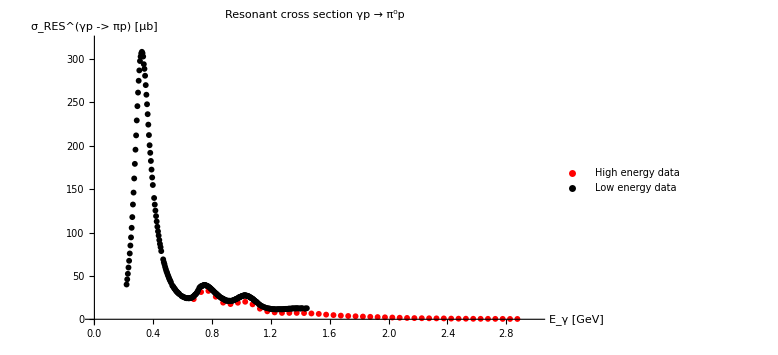

```mathematica
ListPlot[{X,Y},PlotRange->{{0,3},{0,320}},PlotStyle->{Red,Black},AxesLabel->{"E_γ [GeV]","σ_RES^(γp -> πp) [μb]"},PlotLabel->"Resonant cross section γp → π^0p",ImageSize->Large,PlotLegends->{"High energy data","Low energy data"}]
```

## Calculation

### Amplitude for γp →Δ^+→ π^0 p

This amplitude was computed from the Lagrangian that looks like 
-Graphics-

```mathematica
pionNucleonDeltaGI[pDelta_,pPi0_,muDelta_]:=Module[{α,β,γ},-ⅈ h/(fPi M)*√(2/3)*Eps[LorentzIndex[muDelta],LorentzIndex[α],LorentzIndex[β],LorentzIndex[γ]]GA[γ].GA[5]Pair[Momentum[pPi0],LorentzIndex[α]]Pair[Momentum[pDelta],LorentzIndex[β]]];(* index 3 == pion; index 1 == Nucleon, index 2 == Delta isospinFactor=√(2/3), the gDGI = h from the paper *)
```

("n̄" | 1
"Δ^-" | 2
"π^+" | 3) | ("n̄" | 1
"Δ^+" | 2
"π^-" | 3) | ("p̄" | 1
"Δ^0" | 2
"π^+" | 3) | ("p̄" | 1
"Δ^(++)" | 2
"π^-" | 3) | ("n̄" | 1
"Δ^0" | 2
"π^0" | 3) | ("p̄" | 1
"Δ^+" | 2
"π^0" | 3)
-((ⅈ h ϵ_(("μ")_2,α1,β1,γ1) ("p")_2^β1 ("p")_3^α1 (γ^γ1.γ^5)_(("s")_1,("s")_2))/(MDelta "f_π")) | (ⅈ h ϵ_(("μ")_2,α1,β1,γ1) ("p")_2^β1 ("p")_3^α1 (γ^γ1.γ^5)_(("s")_1,("s")_2))/(√3 MDelta "f_π") | -((ⅈ h ϵ_(("μ")_2,α1,β1,γ1) ("p")_2^β1 ("p")_3^α1 (γ^γ1.γ^5)_(("s")_1,("s")_2))/(√3 MDelta "f_π")) | (ⅈ h ϵ_(("μ")_2,α1,β1,γ1) ("p")_2^β1 ("p")_3^α1 (γ^γ1.γ^5)_(("s")_1,("s")_2))/(MDelta "f_π") | -((ⅈ √(2/3) h ϵ_(("μ")_2,α1,β1,γ1) ("p")_2^β1 ("p")_3^α1 (γ^γ1.γ^5)_(("s")_1,("s")_2))/(MDelta "f_π")) | -((ⅈ √(2/3) h ϵ_(("μ")_2,α1,β1,γ1) ("p")_2^β1 ("p")_3^α1 (γ^γ1.γ^5)_(("s")_1,("s")_2))/(MDelta "f_π"))
("OverBar[Δ^0]" | 1
"n" | 2
"π^0" | 3) | ("OverBar[Δ^-]" | 1
"n" | 2
"π^-" | 3) | ("OverBar[Δ^+]" | 1
"n" | 2
"π^+" | 3) | ("OverBar[Δ^0]" | 1
"p" | 2
"π^-" | 3) | ("OverBar[Δ^+]" | 1
"p" | 2
"π^0" | 3) | ("OverBar[Δ^(++)]" | 1
"p" | 2
"π^+" | 3)
-((ⅈ √(2/3) h ϵ_(("μ")_1,α1,β1,γ1) ("p")_1^β1 ("p")_3^α1 (γ^γ1.γ^5)_(("s")_1,("s")_2))/(MDelta "f_π")) | -((ⅈ h ϵ_(("μ")_1,α1,β1,γ1) ("p")_1^β1 ("p")_3^α1 (γ^γ1.γ^5)_(("s")_1,("s")_2))/(MDelta "f_π")) | (ⅈ h ϵ_(("μ")_1,α1,β1,γ1) ("p")_1^β1 ("p")_3^α1 (γ^γ1.γ^5)_(("s")_1,("s")_2))/(√3 MDelta "f_π") | -((ⅈ h ϵ_(("μ")_1,α1,β1,γ1) ("p")_1^β1 ("p")_3^α1 (γ^γ1.γ^5)_(("s")_1,("s")_2))/(√3 MDelta "f_π")) | -((ⅈ √(2/3) h ϵ_(("μ")_1,α1,β1,γ1) ("p")_1^β1 ("p")_3^α1 (γ^γ1.γ^5)_(("s")_1,("s")_2))/(MDelta "f_π")) | (ⅈ h ϵ_(("μ")_1,α1,β1,γ1) ("p")_1^β1 ("p")_3^α1 (γ^γ1.γ^5)_(("s")_1,("s")_2))/(MDelta "f_π")

```mathematica
DeltaPropagator[p1_,mu_,nu_]:=(GS[Momentum[p1]]+M).(Pair[LorentzIndex[mu],LorentzIndex[nu]]
-1/3 GA[mu].GA[nu]
-(2Pair[LorentzIndex[mu],Momentum[p1]]Pair[LorentzIndex[nu],Momentum[p1]])/(3 M^2)
-1/(3M)(Pair[LorentzIndex[nu],Momentum[p1]]GA[mu]-Pair[LorentzIndex[mu],Momentum[p1]]GA[nu]));
```

```mathematica
γNDelta[κ_,G1_,G2_,p2_,p3_,mu2_,mu3_]:=Kappa Module[{α,β},
-ⅈ √(2/3)G2*Pair[Momentum[p2],LorentzIndex[mu3]]*Pair[Momentum[p3],LorentzIndex[mu2]]GA[5]+2 √(1/6)G1 Eps[LorentzIndex[mu2],LorentzIndex[mu3],LorentzIndex[α],LorentzIndex[β]]*Pair[Momentum[p2],LorentzIndex[α]]*Pair[Momentum[p3],LorentzIndex[β]]+ⅈ √(2/3)G2 Pair[LorentzIndex[mu2],LorentzIndex[mu3]]Pair[Momentum[p3],Momentum[p2]]GA[5]
](*1 - Proton, 2 - Delta, 3 - Photon Kappa = (3e)/(2MN(MN+MDelta))*)
```

### Squared averaged amplitudes for γp →Δ^+→ π^0 p

p_1-γ
p_2-P
p_3-π
p_4-P

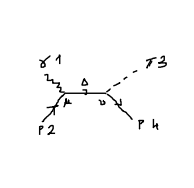

```mathematica
(* pionNucleonDeltaGI[pDelta_,pPi0_,muDelta_] and γNDelta[κ_,G1_,G2_,pDelta_,pGamma_,muDelta_,muGamma_] *)
```

```mathematica
As=FCRenameDummyIndices[SpinorUBar[Subscript[p, 4],MN].pionNucleonDeltaGI[Subscript[p, 3]+Subscript[p, 4],-Subscript[p, 3],ν].DeltaPropagator[Subscript[p, 3]+Subscript[p, 4],ν,μ].γNDelta[κ,G1,G2,-(Subscript[p, 3]+Subscript[p, 4]),-Subscript[p, 3],μ,ρ].SpinorU[Subscript[p, 2],MN]]//DiracSimplify//DiracEquation//ExpandScalarProduct//DiracSimplify;
Au=FCRenameDummyIndices[SpinorUBar[Subscript[p, 4],MN].γNDelta[κ,G1,G2,Subscript[p, 4]-Subscript[p, 1],Subscript[p, 1],ν,ρ].DeltaPropagator[Subscript[p, 4]-Subscript[p, 1],ν,μ].pionNucleonDeltaGI[-(Subscript[p, 4]-Subscript[p, 1]),Subscript[p, 3],μ].SpinorU[Subscript[p, 2],MN]]//DiracSimplify//DiracEquation//ExpandScalarProduct//DiracSimplify;(* Subscript[p, delta]=Subscript[p, 1]+Subscript[p, 2]=Subscript[p, 3]+Subscript[p, 4]. *)
```

```mathematica
ASquared[0]=Map[DiracSimplify[FermionSpinSum[DiracEquation[#]]]&,{
-As*ComplexConjugate[As],
-As*ComplexConjugate[Au],
-Au*ComplexConjugate[Au]
}]
```

```mathematica
ASquared[0]=-
```

```mathematica
ASquared[1]=FullSimplify[ASquared[0]/.{u->MPi^2+2 MN^2-s-t}];
```

```mathematica
ASquared[1]={1/(81 fPi^2 M^2)h^2 Kappa^2 (MN^4-2 (MPi^2+s) MN^2+(MPi^2-s)^2) ((MN^4-2 (MPi^2+s) MN^2+(MPi^2-s)^2) ((MN^2+2 M MN+s) (MN^2+2 M MN-MPi^2+s)+(s-M^2) t) G1^2-2 G2 (MN^2-MPi^2-s) (MN^6-(2 MPi^2+s) MN^4+(MPi^4-2 s MPi^2+s (t-s)) MN^2+2 M (MN^4-(MPi^2+2 s) MN^2+s (-MPi^2+s+2 t)) MN+(MPi^2-s) s (MPi^2-s-t)+M^2 ((2 MPi^2+t) MN^2+(s-MPi^2) t)) G1+G2^2 (MN^8-(3 MPi^2+4 s) MN^6+2 M MPi^2 MN^5+(3 MPi^4+7 s MPi^2+M^2 (8 MPi^2-t)+s (6 s+t)) MN^4-4 M MPi^2 (MPi^2+s) MN^3+(2 M^2 (-4 MPi^4+(t-8 s) MPi^2+s t)-(MPi^2+s) (MPi^4+s MPi^2+2 s (2 s+t))) MN^2+2 M MPi^2 (MPi^4+10 s MPi^2+s^2) MN-(MPi^2-s) s (8 M^2 MPi^2+(MPi^2+s)^2)+(s-M^2) (MPi^4-6 s MPi^2+s^2) t)),1/(81 fPi^2 M^2)h^2 Kappa^2 ((3 MN^12-10 (MPi^2+s) MN^10+(6 MPi^4+8 s MPi^2+3 s (3 s+4 t)) MN^8-(MPi^6-3 (5 s+t) MPi^4+4 s (7 t-2 s) MPi^2-4 s (s^2-7 t s-3 t^2)) MN^6+(3 MPi^8-4 (s+t) MPi^6+2 s (3 s-7 t) MPi^4+2 s (2 s-5 t) (s-2 t) MPi^2+s (-11 s^3+20 t s^2+23 t^2 s+4 t^3)) MN^4-(MPi^2-s-t) (MPi^8-2 s MPi^6+s (3 s-2 t) MPi^4-2 s (4 s-3 t) (s-t) MPi^2+2 s^2 (s-2 t) (3 s+t)) MN^2-(MPi^2-s)^2 s (s-2 t) (-MPi^2+s+t)^2+M^2 (4 MN^10+2 (-6 MPi^2-8 s+t) MN^8+(7 MPi^4+4 (3 s-t) MPi^2+4 (3 s-t) (2 s+t)) MN^6+(-4 MPi^6+2 (7 s-t) MPi^4+(12 s^2-26 t s+9 t^2) MPi^2-16 s^3+t^3+3 s t^2-16 s^2 t) MN^4-(MPi^8+2 (s-3 t) MPi^6+(-11 s^2+10 t s+4 t^2) MPi^4+2 (6 s^3+4 t s^2-6 t^2 s+t^3) MPi^2-2 s^2 (2 s^2+6 t s+t^2)) MN^2+(MPi^2-s)^2 (MPi^2-s-t) (2 s-t) t)+2 M (4 MN^11+2 (-6 MPi^2-8 s+t) MN^9+(7 MPi^4+4 (3 s-t) MPi^2+4 (3 s-t) (2 s+t)) MN^7+(-4 MPi^6+2 (7 s-t) MPi^4+(12 s^2-26 t s+9 t^2) MPi^2-16 s^3+t^3+3 s t^2-16 s^2 t) MN^5-(MPi^8+2 (s-3 t) MPi^6+(-11 s^2+10 t s+4 t^2) MPi^4+2 (6 s^3+4 t s^2-6 t^2 s+t^3) MPi^2-2 s^2 (2 s^2+6 t s+t^2)) MN^3+(MPi^2-s)^2 (MPi^2-s-t) (2 s-t) t MN)) G1^2-2 G2 (MN^12+(-3 MPi^2-6 s+t) MN^10+M (MPi^2+3 t) MN^9+(2 MPi^4+(11 s-6 t) MPi^2+15 s^2+2 t^2+s t) MN^8+M (MPi^4-2 s MPi^2+5 t (t-2 s)) MN^7-(5 MPi^6-(s+12 t) MPi^4+2 (6 s^2+t (t-4 M^2)) MPi^2+20 s^3+t^3+(2 s-3 M^2) t^2+12 s^2 t) MN^6+M (2 MPi^6+(5 t-3 s) MPi^4-2 t (5 s+3 t) MPi^2-t (-12 s^2+t s+3 t^2)) MN^5+(5 MPi^8-5 (s+t) MPi^6+(-11 s^2+3 t s-3 t^2) MPi^4+t (8 s^2-3 t s+2 t^2) MPi^2+s (15 s^3+20 t s^2+2 t^2 s+3 t^3)+M^2 (8 MPi^6+2 (s-2 t) MPi^4-t (14 s+9 t) MPi^2-t^2 (s+t))) MN^4+M (2 MPi^8-3 (3 s+t) MPi^6-(s^2-11 t s+3 t^2) MPi^4+(2 s^3+20 t s^2-5 t^2 s+4 t^3) MPi^2+s t (-6 s^2-9 t s+7 t^2)) MN^3+(2 (s-t) MPi^8+(-8 s^2-2 t s+3 t^2) MPi^6+(5 s^3+11 t s^2+3 t^2 s-t^3) MPi^4+s (7 s^3+4 t s^2-7 t^2 s-t^3) MPi^2-s (s+t) (6 s^3+7 t s^2-3 t^2 s+t^3)+M^2 (MPi^8+(s-7 t) MPi^6-(s-t) (2 s+5 t) MPi^4+t (8 s^2+7 t s+2 t^2) MPi^2+s t^2 (t-5 s))) MN^2+M (MPi^2-s-t) (2 s t^3+(MPi^4-s MPi^2-4 s^2) t^2-(MPi^6-8 s^2 MPi^2+s^3) t+s (MPi^3-MPi s)^2) MN-(MPi^2-s) (MPi^2-s-t) (MPi^2 (s^3+2 M^2 t s-(M^2+s) t^2)-s (s^3+2 t s^2+(3 M^2-t) t^2))) G1-G2^2 (MN^12-2 (2 MPi^2+3 s+t) MN^10+2 M (MPi^2+t) MN^9+(2 MPi^4+2 (7 s+6 t) MPi^2+15 s^2-4 t^2+M^2 (4 MPi^2-6 t)+14 s t) MN^8+2 M (2 MPi^4-4 (s+2 t) MPi^2-t (4 s+t)) MN^7+(9 MPi^6+5 s MPi^4-16 s^2 MPi^2-20 s^3+2 t^3+4 (MPi^2+4 s) t^2-3 (MPi^2+2 s) (7 MPi^2+6 s) t+M^2 (-17 MPi^4-16 s MPi^2+10 t^2+24 (MPi^2+s) t)) MN^6+2 M (-12 MPi^6+(9 t-5 s) MPi^4+3 (2 s^2+6 t s+3 t^2) MPi^2+2 s t (3 s+2 t)) MN^5+(-7 MPi^8+(6 t-22 s) MPi^6+(-16 s^2+40 t s+6 t^2) MPi^4+2 (2 s^3+43 t s^2+7 t^2 s-2 t^3) MPi^2+s (15 s^3+44 t s^2-17 t^2 s-22 t^3)+M^2 (20 MPi^6+(26 s-2 t) MPi^4+(24 s^2-30 t s-25 t^2) MPi^2-t (36 s^2+35 t s+t^2))) MN^4-2 M (3 MPi^8+(5 s-13 t) MPi^6+(-4 s^2-11 t s+9 t^2) MPi^4+(4 s^3+12 t s^2+13 t^2 s+2 t^3) MPi^2+s t (s+t) (4 s+t)) MN^3+(-MPi^10+(5 t-9 s) MPi^8+(3 s^2+40 t s-6 t^2) MPi^6+(9 s^3+33 t s^2-54 t^2 s+2 t^3) MPi^4+2 s (2 s^3-20 t s^2-35 t^2 s+8 t^3) MPi^2-2 s (s+t) (3 s^3+10 t s^2-11 t^2 s-3 t^3)+M^2 (5 MPi^8+4 (4 s-5 t) MPi^6-(s^2+60 t s-14 t^2) MPi^4+2 (-8 s^3-6 t s^2+23 t^2 s+t^3) MPi^2+2 s t (12 s^2+20 t s+5 t^2))) MN^2+2 M ((t-s) MPi^8+(s^2+4 t s-3 t^2) MPi^6-(s^3+4 t s^2+5 t^2 s-2 t^3) MPi^4+s (s+t) (s^2+t s+3 t^2) MPi^2+s^2 t (s+t)^2) MN+(MPi^2-s-t) (((4 s^2-10 t s+t^2) MPi^4-2 s (2 s^2+4 t s-7 t^2) MPi^2+3 s^2 t (2 s+3 t)) M^2+s (6 (MPi^2+s) t^3+2 (-4 MPi^4-9 s MPi^2+s^2) t^2+(MPi^2-s) (2 MPi^4+13 s MPi^2+5 s^2) t-(MPi^2-s)^2 s (MPi^2+s))))),1/(81 fPi^2 M^2)h^2 Kappa^2 ((9 MN^12-(15 MPi^2+42 s+124 t) MN^10+(-153 MPi^4+(17 s-4 t) MPi^2+79 s^2+208 t^2+383 s t) MN^8-(159 MPi^6-2 (85 s+149 t) MPi^4+(-26 s^2-306 t s+8 t^2) MPi^2+76 s^3+132 t^3+628 s t^2+428 s^2 t) MN^6-(MPi^2-s-t) (42 MPi^6-(37 s+124 t) MPi^4+(-7 s^2-176 t s+47 t^2) MPi^2+39 s^3+37 t^3+377 s t^2+163 s^2 t) MN^4-(-MPi^2+s+t)^2 (2 (s-6 t) MPi^4-(s^2+40 t s-9 t^2) MPi^2+2 (5 s^3+6 t s^2+57 t^2 s+2 t^3)) MN^2+2 M (6 MN^2+MPi^2-2 (s+t)) (MN^8-2 (MPi^2+2 s+8 t) MN^6+(-19 MPi^4+2 (s+4 t) MPi^2+6 (s^2+7 t s+2 t^2)) MN^4-2 (MPi^2-s-t) (5 MPi^4-(s+4 t) MPi^2-2 (s^2+8 t s+t^2)) MN^2+(-MPi^2+s+t)^2 (s^2+8 t s+t^2)) MN+s (-MPi^2+s+t)^3 (s^2-4 t s+13 t^2)+M^2 (4 MN^10-(8 MPi^2+16 s+77 t) MN^8+(-88 MPi^4+(8 s+58 t) MPi^2+4 (6 s^2+55 t s+10 t^2)) MN^6-(28 MPi^6-(72 s+55 t) MPi^4-2 (4 s^2+31 t s-6 t^2) MPi^2+2 (8 s^3+111 t s^2+75 t^2 s+8 t^3)) MN^4+2 (MPi^2-s-t) ((6 s-t) MPi^4+(2 s^2+3 t s+4 t^2) MPi^2-2 (s^3+22 t s^2+5 t^2 s+2 t^3)) MN^2-t (-MPi^2+s+t)^2 (13 s^2-4 t s+t^2))) G1^2+2 G2 (MN^2+MPi^2-s-t) (3 MN^10+(-10 MPi^2-13 s+29 t) MN^8+(29 MPi^4+(18 s-19 t) MPi^2+22 s^2-25 t^2-75 s t) MN^6+(14 MPi^6-(9 s+46 t) MPi^4-4 (s^2+12 t s-7 t^2) MPi^2-(s+t) (18 s^2-83 t s-5 t^2)) MN^4+(-MPi^2+s+t) (2 (s+3 t) MPi^4+(s^2+12 t s-7 t^2) MPi^2+7 s (s-5 t) (s+t)) MN^2-s (s-5 t) (s+t) (-MPi^2+s+t)^2+2 M (MN^9-2 (MPi^2+2 (s-5 t)) MN^7+(17 MPi^4+2 (s-5 t) MPi^2+6 (s^2-8 t s-t^2)) MN^5+2 (MPi^2-s-t) (4 MPi^4+(s-5 t) MPi^2+2 (s^2-10 t s+t^2)) MN^3+(-MPi^2+s+t)^2 (s^2-10 t s+t^2) MN)+M^2 ((2 MPi^2+15 t) MN^6+(10 MPi^4-(4 s+11 t) MPi^2+t (t-35 s)) MN^4+(-2 (3 s+t) MPi^4+2 (s^2-5 t s+3 t^2) MPi^2+5 (5 s-t) t (s+t)) MN^2+(MPi^2-s-t) (5 s-t) t (s+t))) G1+G2^2 (MN^12+(-3 MPi^2-6 s+8 t) MN^10+2 M MPi^2 MN^9+(7 MPi^4+3 (3 s-4 t) MPi^2+15 s^2-33 s t+t (48 t-13 M^2)) MN^8-4 M MPi^2 (MPi^2+2 s+8 t) MN^7-(3 MPi^6+2 (5 s-23 t) MPi^4+2 (3 s-4 t) (s+t) MPi^2+2 M^2 (6 MPi^4+4 t^2-13 (MPi^2+2 s) t)+4 (5 s^3-13 t s^2+31 t^2 s+13 t^3)) MN^6+2 M MPi^2 (-19 MPi^4+2 (s+4 t) MPi^2+6 (s^2+7 t s+2 t^2)) MN^5+(M^2 (12 MPi^6+(24 s-17 t) MPi^4+2 t (2 t-13 s) MPi^2-6 s t (13 s+t))-(MPi^2-s-t) (2 MPi^6+(11 s-52 t) MPi^4+3 (3 s^2-8 t s+13 t^2) MPi^2+15 s^3+13 t^3+161 s t^2-53 s^2 t)) MN^4-4 M MPi^2 (MPi^2-s-t) (5 MPi^4-(s+4 t) MPi^2-2 (s^2+8 t s+t^2)) MN^3-(MPi^2-s-t) (2 ((t-6 s) MPi^4+(13 s-2 t) t MPi^2+2 t (13 s^2-4 t s+t^2)) M^2+(MPi^2-s-t) (2 (s-6 t) MPi^4+(3 s^2-8 t s+13 t^2) MPi^2+6 s (s^2-4 t s+13 t^2))) MN^2+2 M MPi^2 (-MPi^2+s+t)^2 (s^2+8 t s+t^2) MN-(-MPi^2+s+t)^2 (-s^4+(13 M^2+3 s) t s^2-(4 M^2+9 s) t^2 s+MPi^2 (s^2-4 t s+13 t^2) s+(M^2-13 s) t^3)))};
```

```mathematica
PropagatorDenominators=({1/(SP[Subscript[p, 1]+Subscript[p, 2],Subscript[p, 1]+Subscript[p, 2]]-M^2+ⅈ M Γs)1/(SP[Subscript[p, 1]+Subscript[p, 2],Subscript[p, 1]+Subscript[p, 2]]-M^2-ⅈ M Γs),1/(SP[Subscript[p, 1]+Subscript[p, 2],Subscript[p, 1]+Subscript[p, 2]]-M^2+ⅈ M Γs)1/(SP[Subscript[p, 4]-Subscript[p, 1],Subscript[p, 4]-Subscript[p, 1]]-M^2-ⅈ M Γu),1/(SP[Subscript[p, 4]-Subscript[p, 1],Subscript[p, 4]-Subscript[p, 1]]-M^2+ⅈ M Γu)1/(SP[Subscript[p, 4]-Subscript[p, 1],Subscript[p, 4]-Subscript[p, 1]]-M^2-ⅈ M Γu)}//ScalarProductExpand//FullSimplify)
```

{1/(Γs^2 M^2+(M^2-s)^2),1/((M^2-ⅈ Γs M-s) (M^2+ⅈ Γu M-u)),1/(Γu^2 M^2+(M^2-u)^2)}

```mathematica
squaredAmplitudesFinal=(ASquared[1]*PropagatorDenominators)/.{u->MPi^2+2 MN^2-s-t}//Simplify;
squaredAmplitudesFinal[[2]]=squaredAmplitudesFinal[[2]]+ComplexConjugate[squaredAmplitudesFinal[[2]]];
squaredAmplitudesFinal=squaredAmplitudesFinal//FullSimplify
```

```mathematica
amplitudeSquaredFunctionSchannel[s_,t_,G1_,G2_,fPi_,Kappa_,h_,MN_,MPi_,M_,Γs_,Γu_]:=1/(81 fPi^2 M^2 ((M^2-s)^2+M^2 Γs^2))h^2 Kappa^2 (MN^4-2 (MPi^2+s) MN^2+(MPi^2-s)^2) ((MN^4-2 (MPi^2+s) MN^2+(MPi^2-s)^2) ((MN^2+2 M MN+s) (MN^2+2 M MN-MPi^2+s)+(s-M^2) t) G1^2-2 G2 (MN^2-MPi^2-s) (MN^6-(2 MPi^2+s) MN^4+(MPi^4-2 s MPi^2+s (t-s)) MN^2+2 M (MN^4-(MPi^2+2 s) MN^2+s (-MPi^2+s+2 t)) MN+(MPi^2-s) s (MPi^2-s-t)+M^2 ((2 MPi^2+t) MN^2+(s-MPi^2) t)) G1+G2^2 (MN^8-(3 MPi^2+4 s) MN^6+2 M MPi^2 MN^5+(3 MPi^4+7 s MPi^2+M^2 (8 MPi^2-t)+s (6 s+t)) MN^4-4 M MPi^2 (MPi^2+s) MN^3+(2 M^2 (-4 MPi^4+(t-8 s) MPi^2+s t)-(MPi^2+s) (MPi^4+s MPi^2+2 s (2 s+t))) MN^2+2 M MPi^2 (MPi^4+10 s MPi^2+s^2) MN-(MPi^2-s) s (8 M^2 MPi^2+(MPi^2+s)^2)+(s-M^2) (MPi^4-6 s MPi^2+s^2) t));
amplitudeSquaredFunctionSUchannel[s_,t_,G1_,G2_,fPi_,Kappa_,h_,MN_,MPi_,M_,Γs_,Γu_]:=(2 h^2 Kappa^2 ((3 MN^12-10 (MPi^2+s) MN^10+(6 MPi^4+8 s MPi^2+3 s (3 s+4 t)) MN^8-(MPi^6-3 (5 s+t) MPi^4+4 s (7 t-2 s) MPi^2-4 s (s^2-7 t s-3 t^2)) MN^6+(3 MPi^8-4 (s+t) MPi^6+2 s (3 s-7 t) MPi^4+2 s (2 s-5 t) (s-2 t) MPi^2+s (-11 s^3+20 t s^2+23 t^2 s+4 t^3)) MN^4-(MPi^2-s-t) (MPi^8-2 s MPi^6+s (3 s-2 t) MPi^4-2 s (4 s-3 t) (s-t) MPi^2+2 s^2 (s-2 t) (3 s+t)) MN^2-(MPi^2-s)^2 s (s-2 t) (-MPi^2+s+t)^2+M^2 (4 MN^10+2 (-6 MPi^2-8 s+t) MN^8+(7 MPi^4+4 (3 s-t) MPi^2+4 (3 s-t) (2 s+t)) MN^6+(-4 MPi^6+2 (7 s-t) MPi^4+(12 s^2-26 t s+9 t^2) MPi^2-16 s^3+t^3+3 s t^2-16 s^2 t) MN^4-(MPi^8+2 (s-3 t) MPi^6+(-11 s^2+10 t s+4 t^2) MPi^4+2 (6 s^3+4 t s^2-6 t^2 s+t^3) MPi^2-2 s^2 (2 s^2+6 t s+t^2)) MN^2+(MPi^2-s)^2 (MPi^2-s-t) (2 s-t) t)+2 M (4 MN^11+2 (-6 MPi^2-8 s+t) MN^9+(7 MPi^4+4 (3 s-t) MPi^2+4 (3 s-t) (2 s+t)) MN^7+(-4 MPi^6+2 (7 s-t) MPi^4+(12 s^2-26 t s+9 t^2) MPi^2-16 s^3+t^3+3 s t^2-16 s^2 t) MN^5-(MPi^8+2 (s-3 t) MPi^6+(-11 s^2+10 t s+4 t^2) MPi^4+2 (6 s^3+4 t s^2-6 t^2 s+t^3) MPi^2-2 s^2 (2 s^2+6 t s+t^2)) MN^3+(MPi^2-s)^2 (MPi^2-s-t) (2 s-t) t MN)) G1^2-2 G2 (MN^12+(-3 MPi^2-6 s+t) MN^10+M (MPi^2+3 t) MN^9+(2 MPi^4+(11 s-6 t) MPi^2+15 s^2+2 t^2+s t) MN^8+M (MPi^4-2 s MPi^2+5 t (t-2 s)) MN^7-(5 MPi^6-(s+12 t) MPi^4+2 (6 s^2+t (t-4 M^2)) MPi^2+20 s^3+t^3+(2 s-3 M^2) t^2+12 s^2 t) MN^6+M (2 MPi^6+(5 t-3 s) MPi^4-2 t (5 s+3 t) MPi^2-t (-12 s^2+t s+3 t^2)) MN^5+(5 MPi^8-5 (s+t) MPi^6+(-11 s^2+3 t s-3 t^2) MPi^4+t (8 s^2-3 t s+2 t^2) MPi^2+s (15 s^3+20 t s^2+2 t^2 s+3 t^3)+M^2 (8 MPi^6+2 (s-2 t) MPi^4-t (14 s+9 t) MPi^2-t^2 (s+t))) MN^4+M (2 MPi^8-3 (3 s+t) MPi^6-(s^2-11 t s+3 t^2) MPi^4+(2 s^3+20 t s^2-5 t^2 s+4 t^3) MPi^2+s t (-6 s^2-9 t s+7 t^2)) MN^3+(2 (s-t) MPi^8+(-8 s^2-2 t s+3 t^2) MPi^6+(5 s^3+11 t s^2+3 t^2 s-t^3) MPi^4+s (7 s^3+4 t s^2-7 t^2 s-t^3) MPi^2-s (s+t) (6 s^3+7 t s^2-3 t^2 s+t^3)+M^2 (MPi^8+(s-7 t) MPi^6-(s-t) (2 s+5 t) MPi^4+t (8 s^2+7 t s+2 t^2) MPi^2+s t^2 (t-5 s))) MN^2+M (MPi^2-s-t) (2 s t^3+(MPi^4-s MPi^2-4 s^2) t^2-(MPi^6-8 s^2 MPi^2+s^3) t+s (MPi^3-MPi s)^2) MN-(MPi^2-s) (MPi^2-s-t) (MPi^2 (s^3+2 M^2 t s-(M^2+s) t^2)-s (s^3+2 t s^2+(3 M^2-t) t^2))) G1-G2^2 (MN^12-2 (2 MPi^2+3 s+t) MN^10+2 M (MPi^2+t) MN^9+(2 MPi^4+2 (7 s+6 t) MPi^2+15 s^2-4 t^2+M^2 (4 MPi^2-6 t)+14 s t) MN^8+2 M (2 MPi^4-4 (s+2 t) MPi^2-t (4 s+t)) MN^7+(9 MPi^6+5 s MPi^4-16 s^2 MPi^2-20 s^3+2 t^3+4 (MPi^2+4 s) t^2-3 (MPi^2+2 s) (7 MPi^2+6 s) t+M^2 (-17 MPi^4-16 s MPi^2+10 t^2+24 (MPi^2+s) t)) MN^6+2 M (-12 MPi^6+(9 t-5 s) MPi^4+3 (2 s^2+6 t s+3 t^2) MPi^2+2 s t (3 s+2 t)) MN^5+(-7 MPi^8+(6 t-22 s) MPi^6+(-16 s^2+40 t s+6 t^2) MPi^4+2 (2 s^3+43 t s^2+7 t^2 s-2 t^3) MPi^2+s (15 s^3+44 t s^2-17 t^2 s-22 t^3)+M^2 (20 MPi^6+(26 s-2 t) MPi^4+(24 s^2-30 t s-25 t^2) MPi^2-t (36 s^2+35 t s+t^2))) MN^4-2 M (3 MPi^8+(5 s-13 t) MPi^6+(-4 s^2-11 t s+9 t^2) MPi^4+(4 s^3+12 t s^2+13 t^2 s+2 t^3) MPi^2+s t (s+t) (4 s+t)) MN^3+(-MPi^10+(5 t-9 s) MPi^8+(3 s^2+40 t s-6 t^2) MPi^6+(9 s^3+33 t s^2-54 t^2 s+2 t^3) MPi^4+2 s (2 s^3-20 t s^2-35 t^2 s+8 t^3) MPi^2-2 s (s+t) (3 s^3+10 t s^2-11 t^2 s-3 t^3)+M^2 (5 MPi^8+4 (4 s-5 t) MPi^6-(s^2+60 t s-14 t^2) MPi^4+2 (-8 s^3-6 t s^2+23 t^2 s+t^3) MPi^2+2 s t (12 s^2+20 t s+5 t^2))) MN^2+2 M ((t-s) MPi^8+(s^2+4 t s-3 t^2) MPi^6-(s^3+4 t s^2+5 t^2 s-2 t^3) MPi^4+s (s+t) (s^2+t s+3 t^2) MPi^2+s^2 t (s+t)^2) MN+(MPi^2-s-t) (((4 s^2-10 t s+t^2) MPi^4-2 s (2 s^2+4 t s-7 t^2) MPi^2+3 s^2 t (2 s+3 t)) M^2+s (6 (MPi^2+s) t^3+2 (-4 MPi^4-9 s MPi^2+s^2) t^2+(MPi^2-s) (2 MPi^4+13 s MPi^2+5 s^2) t-(MPi^2-s)^2 s (MPi^2+s))))) (Γs Γu M^2+(M^2-s) (M^2-2 MN^2-MPi^2+s+t)))/(81 fPi^2 M^2 (M^2-ⅈ Γs M-s) (M^2+ⅈ Γs M-s) (M^2-ⅈ Γu M-2 MN^2-MPi^2+s+t) (M^2+ⅈ Γu M-2 MN^2-MPi^2+s+t));
amplitudeSquaredFunctionUchannel[s_,t_,G1_,G2_,fPi_,Kappa_,h_,MN_,MPi_,M_,Γs_,Γu_]:=1/(81 fPi^2 M^2 ((M^2-2 MN^2-MPi^2+s+t)^2+M^2 Γu^2))h^2 Kappa^2 ((9 MN^12-(15 MPi^2+42 s+124 t) MN^10+(-153 MPi^4+(17 s-4 t) MPi^2+79 s^2+208 t^2+383 s t) MN^8-(159 MPi^6-2 (85 s+149 t) MPi^4+(-26 s^2-306 t s+8 t^2) MPi^2+76 s^3+132 t^3+628 s t^2+428 s^2 t) MN^6-(MPi^2-s-t) (42 MPi^6-(37 s+124 t) MPi^4+(-7 s^2-176 t s+47 t^2) MPi^2+39 s^3+37 t^3+377 s t^2+163 s^2 t) MN^4-(-MPi^2+s+t)^2 (2 (s-6 t) MPi^4-(s^2+40 t s-9 t^2) MPi^2+2 (5 s^3+6 t s^2+57 t^2 s+2 t^3)) MN^2+2 M (6 MN^2+MPi^2-2 (s+t)) (MN^8-2 (MPi^2+2 s+8 t) MN^6+(-19 MPi^4+2 (s+4 t) MPi^2+6 (s^2+7 t s+2 t^2)) MN^4-2 (MPi^2-s-t) (5 MPi^4-(s+4 t) MPi^2-2 (s^2+8 t s+t^2)) MN^2+(-MPi^2+s+t)^2 (s^2+8 t s+t^2)) MN+s (-MPi^2+s+t)^3 (s^2-4 t s+13 t^2)+M^2 (4 MN^10-(8 MPi^2+16 s+77 t) MN^8+(-88 MPi^4+(8 s+58 t) MPi^2+4 (6 s^2+55 t s+10 t^2)) MN^6-(28 MPi^6-(72 s+55 t) MPi^4-2 (4 s^2+31 t s-6 t^2) MPi^2+2 (8 s^3+111 t s^2+75 t^2 s+8 t^3)) MN^4+2 (MPi^2-s-t) ((6 s-t) MPi^4+(2 s^2+3 t s+4 t^2) MPi^2-2 (s^3+22 t s^2+5 t^2 s+2 t^3)) MN^2-t (-MPi^2+s+t)^2 (13 s^2-4 t s+t^2))) G1^2+2 G2 (MN^2+MPi^2-s-t) (3 MN^10+(-10 MPi^2-13 s+29 t) MN^8+(29 MPi^4+(18 s-19 t) MPi^2+22 s^2-25 t^2-75 s t) MN^6+(14 MPi^6-(9 s+46 t) MPi^4-4 (s^2+12 t s-7 t^2) MPi^2-(s+t) (18 s^2-83 t s-5 t^2)) MN^4+(-MPi^2+s+t) (2 (s+3 t) MPi^4+(s^2+12 t s-7 t^2) MPi^2+7 s (s-5 t) (s+t)) MN^2-s (s-5 t) (s+t) (-MPi^2+s+t)^2+2 M (MN^9-2 (MPi^2+2 (s-5 t)) MN^7+(17 MPi^4+2 (s-5 t) MPi^2+6 (s^2-8 t s-t^2)) MN^5+2 (MPi^2-s-t) (4 MPi^4+(s-5 t) MPi^2+2 (s^2-10 t s+t^2)) MN^3+(-MPi^2+s+t)^2 (s^2-10 t s+t^2) MN)+M^2 ((2 MPi^2+15 t) MN^6+(10 MPi^4-(4 s+11 t) MPi^2+t (t-35 s)) MN^4+(-2 (3 s+t) MPi^4+2 (s^2-5 t s+3 t^2) MPi^2+5 (5 s-t) t (s+t)) MN^2+(MPi^2-s-t) (5 s-t) t (s+t))) G1+G2^2 (MN^12+(-3 MPi^2-6 s+8 t) MN^10+2 M MPi^2 MN^9+(7 MPi^4+3 (3 s-4 t) MPi^2+15 s^2-33 s t+t (48 t-13 M^2)) MN^8-4 M MPi^2 (MPi^2+2 s+8 t) MN^7-(3 MPi^6+2 (5 s-23 t) MPi^4+2 (3 s-4 t) (s+t) MPi^2+2 M^2 (6 MPi^4+4 t^2-13 (MPi^2+2 s) t)+4 (5 s^3-13 t s^2+31 t^2 s+13 t^3)) MN^6+2 M MPi^2 (-19 MPi^4+2 (s+4 t) MPi^2+6 (s^2+7 t s+2 t^2)) MN^5+(M^2 (12 MPi^6+(24 s-17 t) MPi^4+2 t (2 t-13 s) MPi^2-6 s t (13 s+t))-(MPi^2-s-t) (2 MPi^6+(11 s-52 t) MPi^4+3 (3 s^2-8 t s+13 t^2) MPi^2+15 s^3+13 t^3+161 s t^2-53 s^2 t)) MN^4-4 M MPi^2 (MPi^2-s-t) (5 MPi^4-(s+4 t) MPi^2-2 (s^2+8 t s+t^2)) MN^3-(MPi^2-s-t) (2 ((t-6 s) MPi^4+(13 s-2 t) t MPi^2+2 t (13 s^2-4 t s+t^2)) M^2+(MPi^2-s-t) (2 (s-6 t) MPi^4+(3 s^2-8 t s+13 t^2) MPi^2+6 s (s^2-4 t s+13 t^2))) MN^2+2 M MPi^2 (-MPi^2+s+t)^2 (s^2+8 t s+t^2) MN-(-MPi^2+s+t)^2 (-s^4+(13 M^2+3 s) t s^2-(4 M^2+9 s) t^2 s+MPi^2 (s^2-4 t s+13 t^2) s+(M^2-13 s) t^3)));
```

```mathematica
amplitudeSquaredFunction[s_,t_,G1_,G2_,fPi_,Kappa_,h_,MN_,MPi_,M_,Γs_,Γu_]:={1/(81 fPi^2 M^2 ((M^2-s)^2+M^2 Γs^2))h^2 Kappa^2 (MN^4-2 (MPi^2+s) MN^2+(MPi^2-s)^2) ((MN^4-2 (MPi^2+s) MN^2+(MPi^2-s)^2) ((MN^2+2 M MN+s) (MN^2+2 M MN-MPi^2+s)+(s-M^2) t) G1^2-2 G2 (MN^2-MPi^2-s) (MN^6-(2 MPi^2+s) MN^4+(MPi^4-2 s MPi^2+s (t-s)) MN^2+2 M (MN^4-(MPi^2+2 s) MN^2+s (-MPi^2+s+2 t)) MN+(MPi^2-s) s (MPi^2-s-t)+M^2 ((2 MPi^2+t) MN^2+(s-MPi^2) t)) G1+G2^2 (MN^8-(3 MPi^2+4 s) MN^6+2 M MPi^2 MN^5+(3 MPi^4+7 s MPi^2+M^2 (8 MPi^2-t)+s (6 s+t)) MN^4-4 M MPi^2 (MPi^2+s) MN^3+(2 M^2 (-4 MPi^4+(t-8 s) MPi^2+s t)-(MPi^2+s) (MPi^4+s MPi^2+2 s (2 s+t))) MN^2+2 M MPi^2 (MPi^4+10 s MPi^2+s^2) MN-(MPi^2-s) s (8 M^2 MPi^2+(MPi^2+s)^2)+(s-M^2) (MPi^4-6 s MPi^2+s^2) t)),(2 h^2 Kappa^2 ((3 MN^12-10 (MPi^2+s) MN^10+(6 MPi^4+8 s MPi^2+3 s (3 s+4 t)) MN^8-(MPi^6-3 (5 s+t) MPi^4+4 s (7 t-2 s) MPi^2-4 s (s^2-7 t s-3 t^2)) MN^6+(3 MPi^8-4 (s+t) MPi^6+2 s (3 s-7 t) MPi^4+2 s (2 s-5 t) (s-2 t) MPi^2+s (-11 s^3+20 t s^2+23 t^2 s+4 t^3)) MN^4-(MPi^2-s-t) (MPi^8-2 s MPi^6+s (3 s-2 t) MPi^4-2 s (4 s-3 t) (s-t) MPi^2+2 s^2 (s-2 t) (3 s+t)) MN^2-(MPi^2-s)^2 s (s-2 t) (-MPi^2+s+t)^2+M^2 (4 MN^10+2 (-6 MPi^2-8 s+t) MN^8+(7 MPi^4+4 (3 s-t) MPi^2+4 (3 s-t) (2 s+t)) MN^6+(-4 MPi^6+2 (7 s-t) MPi^4+(12 s^2-26 t s+9 t^2) MPi^2-16 s^3+t^3+3 s t^2-16 s^2 t) MN^4-(MPi^8+2 (s-3 t) MPi^6+(-11 s^2+10 t s+4 t^2) MPi^4+2 (6 s^3+4 t s^2-6 t^2 s+t^3) MPi^2-2 s^2 (2 s^2+6 t s+t^2)) MN^2+(MPi^2-s)^2 (MPi^2-s-t) (2 s-t) t)+2 M (4 MN^11+2 (-6 MPi^2-8 s+t) MN^9+(7 MPi^4+4 (3 s-t) MPi^2+4 (3 s-t) (2 s+t)) MN^7+(-4 MPi^6+2 (7 s-t) MPi^4+(12 s^2-26 t s+9 t^2) MPi^2-16 s^3+t^3+3 s t^2-16 s^2 t) MN^5-(MPi^8+2 (s-3 t) MPi^6+(-11 s^2+10 t s+4 t^2) MPi^4+2 (6 s^3+4 t s^2-6 t^2 s+t^3) MPi^2-2 s^2 (2 s^2+6 t s+t^2)) MN^3+(MPi^2-s)^2 (MPi^2-s-t) (2 s-t) t MN)) G1^2-2 G2 (MN^12+(-3 MPi^2-6 s+t) MN^10+M (MPi^2+3 t) MN^9+(2 MPi^4+(11 s-6 t) MPi^2+15 s^2+2 t^2+s t) MN^8+M (MPi^4-2 s MPi^2+5 t (t-2 s)) MN^7-(5 MPi^6-(s+12 t) MPi^4+2 (6 s^2+t (t-4 M^2)) MPi^2+20 s^3+t^3+(2 s-3 M^2) t^2+12 s^2 t) MN^6+M (2 MPi^6+(5 t-3 s) MPi^4-2 t (5 s+3 t) MPi^2-t (-12 s^2+t s+3 t^2)) MN^5+(5 MPi^8-5 (s+t) MPi^6+(-11 s^2+3 t s-3 t^2) MPi^4+t (8 s^2-3 t s+2 t^2) MPi^2+s (15 s^3+20 t s^2+2 t^2 s+3 t^3)+M^2 (8 MPi^6+2 (s-2 t) MPi^4-t (14 s+9 t) MPi^2-t^2 (s+t))) MN^4+M (2 MPi^8-3 (3 s+t) MPi^6-(s^2-11 t s+3 t^2) MPi^4+(2 s^3+20 t s^2-5 t^2 s+4 t^3) MPi^2+s t (-6 s^2-9 t s+7 t^2)) MN^3+(2 (s-t) MPi^8+(-8 s^2-2 t s+3 t^2) MPi^6+(5 s^3+11 t s^2+3 t^2 s-t^3) MPi^4+s (7 s^3+4 t s^2-7 t^2 s-t^3) MPi^2-s (s+t) (6 s^3+7 t s^2-3 t^2 s+t^3)+M^2 (MPi^8+(s-7 t) MPi^6-(s-t) (2 s+5 t) MPi^4+t (8 s^2+7 t s+2 t^2) MPi^2+s t^2 (t-5 s))) MN^2+M (MPi^2-s-t) (2 s t^3+(MPi^4-s MPi^2-4 s^2) t^2-(MPi^6-8 s^2 MPi^2+s^3) t+s (MPi^3-MPi s)^2) MN-(MPi^2-s) (MPi^2-s-t) (MPi^2 (s^3+2 M^2 t s-(M^2+s) t^2)-s (s^3+2 t s^2+(3 M^2-t) t^2))) G1-G2^2 (MN^12-2 (2 MPi^2+3 s+t) MN^10+2 M (MPi^2+t) MN^9+(2 MPi^4+2 (7 s+6 t) MPi^2+15 s^2-4 t^2+M^2 (4 MPi^2-6 t)+14 s t) MN^8+2 M (2 MPi^4-4 (s+2 t) MPi^2-t (4 s+t)) MN^7+(9 MPi^6+5 s MPi^4-16 s^2 MPi^2-20 s^3+2 t^3+4 (MPi^2+4 s) t^2-3 (MPi^2+2 s) (7 MPi^2+6 s) t+M^2 (-17 MPi^4-16 s MPi^2+10 t^2+24 (MPi^2+s) t)) MN^6+2 M (-12 MPi^6+(9 t-5 s) MPi^4+3 (2 s^2+6 t s+3 t^2) MPi^2+2 s t (3 s+2 t)) MN^5+(-7 MPi^8+(6 t-22 s) MPi^6+(-16 s^2+40 t s+6 t^2) MPi^4+2 (2 s^3+43 t s^2+7 t^2 s-2 t^3) MPi^2+s (15 s^3+44 t s^2-17 t^2 s-22 t^3)+M^2 (20 MPi^6+(26 s-2 t) MPi^4+(24 s^2-30 t s-25 t^2) MPi^2-t (36 s^2+35 t s+t^2))) MN^4-2 M (3 MPi^8+(5 s-13 t) MPi^6+(-4 s^2-11 t s+9 t^2) MPi^4+(4 s^3+12 t s^2+13 t^2 s+2 t^3) MPi^2+s t (s+t) (4 s+t)) MN^3+(-MPi^10+(5 t-9 s) MPi^8+(3 s^2+40 t s-6 t^2) MPi^6+(9 s^3+33 t s^2-54 t^2 s+2 t^3) MPi^4+2 s (2 s^3-20 t s^2-35 t^2 s+8 t^3) MPi^2-2 s (s+t) (3 s^3+10 t s^2-11 t^2 s-3 t^3)+M^2 (5 MPi^8+4 (4 s-5 t) MPi^6-(s^2+60 t s-14 t^2) MPi^4+2 (-8 s^3-6 t s^2+23 t^2 s+t^3) MPi^2+2 s t (12 s^2+20 t s+5 t^2))) MN^2+2 M ((t-s) MPi^8+(s^2+4 t s-3 t^2) MPi^6-(s^3+4 t s^2+5 t^2 s-2 t^3) MPi^4+s (s+t) (s^2+t s+3 t^2) MPi^2+s^2 t (s+t)^2) MN+(MPi^2-s-t) (((4 s^2-10 t s+t^2) MPi^4-2 s (2 s^2+4 t s-7 t^2) MPi^2+3 s^2 t (2 s+3 t)) M^2+s (6 (MPi^2+s) t^3+2 (-4 MPi^4-9 s MPi^2+s^2) t^2+(MPi^2-s) (2 MPi^4+13 s MPi^2+5 s^2) t-(MPi^2-s)^2 s (MPi^2+s))))) (Γs Γu M^2+(M^2-s) (M^2-2 MN^2-MPi^2+s+t)))/(81 fPi^2 M^2 (M^2-ⅈ Γs M-s) (M^2+ⅈ Γs M-s) (M^2-ⅈ Γu M-2 MN^2-MPi^2+s+t) (M^2+ⅈ Γu M-2 MN^2-MPi^2+s+t)),1/(81 fPi^2 M^2 ((M^2-2 MN^2-MPi^2+s+t)^2+M^2 Γu^2))h^2 Kappa^2 ((9 MN^12-(15 MPi^2+42 s+124 t) MN^10+(-153 MPi^4+(17 s-4 t) MPi^2+79 s^2+208 t^2+383 s t) MN^8-(159 MPi^6-2 (85 s+149 t) MPi^4+(-26 s^2-306 t s+8 t^2) MPi^2+76 s^3+132 t^3+628 s t^2+428 s^2 t) MN^6-(MPi^2-s-t) (42 MPi^6-(37 s+124 t) MPi^4+(-7 s^2-176 t s+47 t^2) MPi^2+39 s^3+37 t^3+377 s t^2+163 s^2 t) MN^4-(-MPi^2+s+t)^2 (2 (s-6 t) MPi^4-(s^2+40 t s-9 t^2) MPi^2+2 (5 s^3+6 t s^2+57 t^2 s+2 t^3)) MN^2+2 M (6 MN^2+MPi^2-2 (s+t)) (MN^8-2 (MPi^2+2 s+8 t) MN^6+(-19 MPi^4+2 (s+4 t) MPi^2+6 (s^2+7 t s+2 t^2)) MN^4-2 (MPi^2-s-t) (5 MPi^4-(s+4 t) MPi^2-2 (s^2+8 t s+t^2)) MN^2+(-MPi^2+s+t)^2 (s^2+8 t s+t^2)) MN+s (-MPi^2+s+t)^3 (s^2-4 t s+13 t^2)+M^2 (4 MN^10-(8 MPi^2+16 s+77 t) MN^8+(-88 MPi^4+(8 s+58 t) MPi^2+4 (6 s^2+55 t s+10 t^2)) MN^6-(28 MPi^6-(72 s+55 t) MPi^4-2 (4 s^2+31 t s-6 t^2) MPi^2+2 (8 s^3+111 t s^2+75 t^2 s+8 t^3)) MN^4+2 (MPi^2-s-t) ((6 s-t) MPi^4+(2 s^2+3 t s+4 t^2) MPi^2-2 (s^3+22 t s^2+5 t^2 s+2 t^3)) MN^2-t (-MPi^2+s+t)^2 (13 s^2-4 t s+t^2))) G1^2+2 G2 (MN^2+MPi^2-s-t) (3 MN^10+(-10 MPi^2-13 s+29 t) MN^8+(29 MPi^4+(18 s-19 t) MPi^2+22 s^2-25 t^2-75 s t) MN^6+(14 MPi^6-(9 s+46 t) MPi^4-4 (s^2+12 t s-7 t^2) MPi^2-(s+t) (18 s^2-83 t s-5 t^2)) MN^4+(-MPi^2+s+t) (2 (s+3 t) MPi^4+(s^2+12 t s-7 t^2) MPi^2+7 s (s-5 t) (s+t)) MN^2-s (s-5 t) (s+t) (-MPi^2+s+t)^2+2 M (MN^9-2 (MPi^2+2 (s-5 t)) MN^7+(17 MPi^4+2 (s-5 t) MPi^2+6 (s^2-8 t s-t^2)) MN^5+2 (MPi^2-s-t) (4 MPi^4+(s-5 t) MPi^2+2 (s^2-10 t s+t^2)) MN^3+(-MPi^2+s+t)^2 (s^2-10 t s+t^2) MN)+M^2 ((2 MPi^2+15 t) MN^6+(10 MPi^4-(4 s+11 t) MPi^2+t (t-35 s)) MN^4+(-2 (3 s+t) MPi^4+2 (s^2-5 t s+3 t^2) MPi^2+5 (5 s-t) t (s+t)) MN^2+(MPi^2-s-t) (5 s-t) t (s+t))) G1+G2^2 (MN^12+(-3 MPi^2-6 s+8 t) MN^10+2 M MPi^2 MN^9+(7 MPi^4+3 (3 s-4 t) MPi^2+15 s^2-33 s t+t (48 t-13 M^2)) MN^8-4 M MPi^2 (MPi^2+2 s+8 t) MN^7-(3 MPi^6+2 (5 s-23 t) MPi^4+2 (3 s-4 t) (s+t) MPi^2+2 M^2 (6 MPi^4+4 t^2-13 (MPi^2+2 s) t)+4 (5 s^3-13 t s^2+31 t^2 s+13 t^3)) MN^6+2 M MPi^2 (-19 MPi^4+2 (s+4 t) MPi^2+6 (s^2+7 t s+2 t^2)) MN^5+(M^2 (12 MPi^6+(24 s-17 t) MPi^4+2 t (2 t-13 s) MPi^2-6 s t (13 s+t))-(MPi^2-s-t) (2 MPi^6+(11 s-52 t) MPi^4+3 (3 s^2-8 t s+13 t^2) MPi^2+15 s^3+13 t^3+161 s t^2-53 s^2 t)) MN^4-4 M MPi^2 (MPi^2-s-t) (5 MPi^4-(s+4 t) MPi^2-2 (s^2+8 t s+t^2)) MN^3-(MPi^2-s-t) (2 ((t-6 s) MPi^4+(13 s-2 t) t MPi^2+2 t (13 s^2-4 t s+t^2)) M^2+(MPi^2-s-t) (2 (s-6 t) MPi^4+(3 s^2-8 t s+13 t^2) MPi^2+6 s (s^2-4 t s+13 t^2))) MN^2+2 M MPi^2 (-MPi^2+s+t)^2 (s^2+8 t s+t^2) MN-(-MPi^2+s+t)^2 (-s^4+(13 M^2+3 s) t s^2-(4 M^2+9 s) t^2 s+MPi^2 (s^2-4 t s+13 t^2) s+(M^2-13 s) t^3)))}
```

```mathematica
Join[{{1,2,3},{3,4,5},{6,7,8}},{{1,2,3}}]//InputForm
```

{{1, 2, 3}, {3, 4, 5}, {6, 7, 8}, {1, 2, 3}}

```mathematica
Manipulate[Plot[{
amplitudeSquaredFunctionSchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu],
amplitudeSquaredFunctionSUchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu],
amplitudeSquaredFunctionUchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu],{amplitudeSquaredFunctionSchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu]+amplitudeSquaredFunctionSUchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu]+amplitudeSquaredFunctionUchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu]}},{t,MPi^2-√((MN^4-2 MN^2 s+s^2)/s) √((-2 s (MN^2+MPi^2)+(MPi^2-MN^2)^2+s^2)/s),MPi^2},PlotLegends->{"s channel","s-u mixed","u channel","|s+u|^2"},PlotStyle->Darker/@{Red,Green,Blue,Black},PlotLabel->"√s = "<>ToString[N[√s]]<>" GeV"],{{Kappa,1},0,2},{{Γs,0.102},0.06,0.24},{{Γu,0.102},0.06,0.24},{{s,2},1.01(MN+MPi)^2,5},{{M,1.209},1,8},{{Γ,0.102},0.06,0.24},{{MN,0.938},0,2},{{MPi,0.138},0.1,0.3},{{fPi,0.093},0,1},{{α,1/137},0,2},{{G1,6.061},0.010,10},{{G2,2.414},0.010,10},{{h,0.76},0,10},{{Λ,1.21},0,2},{{isospinFactor,√(2/3)},{√(1/3),1,√(2/3)}}]
```

## Cross sections

### s channel

```mathematica
Clear[crossSectionSchannel];
crossSectionSchannel=Integrate[amplitudeSquaredFunctionSchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu]/(64π s pCOM[s,MN,MPi]^2),{t,tmax[M,MN,MPi,s],tmin[M,MN,MPi,s]}]
```

```mathematica
crossSectionSchannel[s_,G1_,G2_,fPi_,Kappa_,h_,MN_,MPi_,M_,Γs_,Γu_]:=-(h^2*Kappa^2*(G1^2*(MN^2 - s)*(MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s))*(2*s*(2*M*MN + MN^2 + s)*(2*M*MN + MN^2 - MPi^2 + s)*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] - 
     (M^2 - s)*(MN^6 - MN^4*(2*MPi^2 + 3*s) + MN^2*(MPi^4 + 3*s^2) - s*(MPi^4 + s^2 - 2*MPi^2*(s + Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)])))) + 
   G2^2*(2*MN^8*(MN^2 - s)*s*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] + 4*M*MN^5*MPi^2*(MN^2 - s)*s*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] - 
     8*M*MN^3*MPi^2*(MN^2 - s)*s*(MPi^2 + s)*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] - 2*MN^6*(MN^2 - s)*s*(3*MPi^2 + 4*s)*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] + 
     4*M*MN*MPi^2*(MN^2 - s)*s*(MPi^4 + 10*MPi^2*s + s^2)*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] - 2*(MN^2 - s)*(MPi^2 - s)*s^2*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)]*(8*M^2*MPi^2 + (MPi^2 + s)^2) + 
     MN^4*(MN^2 - s)*(MPi^4*(M^2 - s)*(-MN^2 + s) + (M^2 - s)*(-MN^2 + s)^3 + 2*MPi^2*(M^2 - s)*(MN^4 - s^2) + 14*M^2*MPi^2*s*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] + 
       6*MPi^4*s*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] + 16*MPi^2*s^2*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] + 12*s^3*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)]) - 
     2*MN^2*(MN^2 - s)*(s*(MPi^2 + s)*(MN^6 - (MPi^2 - s)^2*s - MN^4*(2*MPi^2 + 3*s) + MN^2*(MPi^4 + 3*s^2) + MPi^4*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] + 3*MPi^2*s*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] + 
         4*s^2*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)]) + M^2*(6*MPi^4*s*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] + 14*MPi^2*s^2*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] - 
         (MN^2 - s)*(MPi^2 + s)*(MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)))) - (M^2 - s)*(MN^2 - s)*(MPi^4 - 6*MPi^2*s + s^2)*(MN^6 - MN^4*(2*MPi^2 + 3*s) + MN^2*(MPi^4 + 3*s^2) - 
       s*(MPi^4 + s^2 - 2*MPi^2*(s + Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)])))) - 2*G1*G2*(MN^2 - s)*(MN^2 - MPi^2 - s)*
    (4*M*MN*(MN^2 - s)*s*(MN^4 + MPi^4 - 2*MPi^2*s + s^2 - MPi^2*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] - s*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] + 
       MN^2*(-2*MPi^2 - 2*s + Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)])) + M^2*(MN^8 + MN^4*MPi^2*(3*MPi^2 + s) - MN^6*(3*MPi^2 + 2*s) - 
       MN^2*(MPi^6 - 2*s^3 + MPi^2*s*(s - 6*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)])) + (MPi^2 - s)*s*(MPi^4 + s^2 - 2*MPi^2*(s + Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)]))) - 
     s*(-MN^8 + MN^6*(3*MPi^2 + 2*s - 2*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)]) - (MPi^2 - s)*s*(MPi^4 - 2*MPi^2*s + s*(s - 2*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)])) + 
       MN^2*(MPi^6 - 2*MPi^4*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] + 2*s^2*(-s + Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)]) + MPi^2*s*(s + 2*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)])) + 
       MN^4*(-3*MPi^4 + 2*s*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)] + MPi^2*(-s + 4*Sqrt[MN^4 + (MPi^2 - s)^2 - 2*MN^2*(MPi^2 + s)]))))))/(2592*fPi^2*M^2*Pi*s^2*((M^2 - s)^2 + M^2*Γs^2));
```

### s/u channel

```mathematica
amplitudeSquaredFunctionSUchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu]//ComplexExpand
```

```mathematica
listOfTerms=amplitudeSquaredFunctionSUchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu]//ComplexExpand//Apart[#,t]&;
```

```mathematica
listOfTerms
```

```mathematica
listOfTerms=List@@Expand[listOfTerms]
```

```mathematica
integrationResult=ParallelTable[Integrate[term,{t,tmax[M,MN,MPi,s],tmin[M,MN,MPi,s]}],{term,listOfTerms}]
```

(2 G1^2 h^2 Kappa^2 M^10 MN^4)/(81 fPi^2 (M^4+Γs^2 M^2-2 M^2 s+s^2)^2)

```mathematica
Clear[crossSectionSUchannel];
crossSectionSchannel=1/(64π s pCOM[s,MN,MPi]^2)Integrate[amplitudeSquaredFunctionSUchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu],{t,tmax[M,MN,MPi,s],tmin[M,MN,MPi,s]}]
```

∫_(tmax(M,MN,MPi,s))^(tmin(M,MN,MPi,s)) (amplitudeSquaredFunctionSUchannel(s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu))/(64 π s (pCOM(s,MN,MPi))^2)ⅆt

```mathematica
crossSectionSUchannel[s_,G1_,G2_,fPi_,Kappa_,h_,MN_,MPi_,M_,Γs_,Γu_]:=;
```

### Plots

```mathematica
Manipulate[Plot[crossSectionSchannel[s,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu],{s,(MN+MPi)^2,2},PlotLegends->{"s channel","s-u mixed","u channel","|s+u|^2"},PlotStyle->Darker/@{Red,Green,Blue,Black},PlotLabel->"√s = "<>ToString[sqrts]],{{Kappa,1},0,2},{{Γs,0.102},0.06,0.24},{{Γu,0.102},0.06,0.24},{{sqrts,2},√(1.01(MN+MPi)^2),5},{{M,1.209},1,8},{{Γ,0.102},0.06,0.24},{{MN,0.938},0,2},{{MPi,0.138},0.1,0.3},{{fPi,0.093},0,1},{{α,1/137},0,2},{{G1,6.061},0.010,10},{{G2,2.414},0.010,10},{{h,0.76},0,10},{{Λ,1.21},0,2},{{isospinFactor,√(2/3)},{√(1/3),1,√(2/3)}}]
```

```mathematica
Manipulate[Plot[{
amplitudeSquaredFunctionSchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu],
amplitudeSquaredFunctionSUchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu],
amplitudeSquaredFunctionUchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu],amplitudeSquaredFunctionSchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu]+amplitudeSquaredFunctionSUchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu]+amplitudeSquaredFunctionUchannel[s,t,G1,G2,fPi,Kappa,h,MN,MPi,M,Γs,Γu]},{t,MPi^2-√((MN^4-2 MN^2 s+s^2)/s) √((-2 s (MN^2+MPi^2)+(MPi^2-MN^2)^2+s^2)/s),MPi^2},PlotLegends->{"s channel","s-u mixed","u channel","|s+u|^2"},PlotStyle->Darker/@{Red,Green,Blue,Black},PlotLabel->"√s = "<>ToString[sqrts]],{{Kappa,1},0,2},{{Γs,0.102},0.06,0.24},{{Γu,0.102},0.06,0.24},{{sqrts,2},√(1.01(MN+MPi)^2),5},{{M,1.209},1,8},{{Γ,0.102},0.06,0.24},{{MN,0.938},0,2},{{MPi,0.138},0.1,0.3},{{fPi,0.093},0,1},{{α,1/137},0,2},{{G1,6.061},0.010,10},{{G2,2.414},0.010,10},{{h,0.76},0,10},{{Λ,1.21},0,2},{{isospinFactor,√(2/3)},{√(1/3),1,√(2/3)}}]
```

Plot::plln: Limiting value 0.019044-√((0.740977-1.79778 s+s^2)/s) √((0.774125-1.75969 s+s^2)/s) in {t,0.019044-√((0.740977-1.79778 s+s^2)/s) √((0.774125-1.75969 s+s^2)/s),0.019044} is not a machine-sized real number.

### Cross section calculation

The differential cross section is given by dσ/dt=(|ℳ|^2)/(64π s p_com^2) or dσ/dCos[θ]=(|ℳ|^2)/(32 π s)p_f/p_i or dσ/dΩ=(|ℳ|^2)/(64 π^2 s)p_f/p_i.

#### Partial XSEC

As a function of angle

```mathematica
pBefore
```

1/2 √((MN^4-2 MN^2 s+s^2)/s)

```mathematica
pAfter
```

1/2 √((-2 s (MN^2+MPi^2)+(MPi^2-MN^2)^2+s^2)/s)

```mathematica
dσdCosθ[s_,costh_,fPi_,M_,Γs_,Γu_,h_,Kappa_,MN_,MPi_,G1_,G2_]:=Module[{t},
t=MPi^2-1/2 √((MN^4-2 MN^2 s+s^2)/s) √(((-MN^2+MPi^2)^2-2 (MN^2+MPi^2) s+s^2)/s)+1/2 √((MN^4-2 MN^2 s+s^2)/s) √(((-MN^2+MPi^2)^2-2 (MN^2+MPi^2) s+s^2)/s) costh;
1/(32π s)*(√((-MN^2+MPi^2)^2-2 (MN^2+MPi^2) s+s^2))/(√(MN^4-2 MN^2 s+s^2))*({1/(81 fPi^2 M^2 ((M^2-s)^2+M^2 Γs^2))h^2 Kappa^2 (MN^4-2 (MPi^2+s) MN^2+(MPi^2-s)^2) ((MN^4-2 (MPi^2+s) MN^2+(MPi^2-s)^2) ((MN^2+2 M MN+s) (MN^2+2 M MN-MPi^2+s)+(s-M^2) t) G1^2-2 G2 (MN^2-MPi^2-s) (MN^6-(2 MPi^2+s) MN^4+(MPi^4-2 s MPi^2+s (t-s)) MN^2+2 M (MN^4-(MPi^2+2 s) MN^2+s (-MPi^2+s+2 t)) MN+(MPi^2-s) s (MPi^2-s-t)+M^2 ((2 MPi^2+t) MN^2+(s-MPi^2) t)) G1+G2^2 (MN^8-(3 MPi^2+4 s) MN^6+2 M MPi^2 MN^5+(3 MPi^4+7 s MPi^2+M^2 (8 MPi^2-t)+s (6 s+t)) MN^4-4 M MPi^2 (MPi^2+s) MN^3+(2 M^2 (-4 MPi^4+(t-8 s) MPi^2+s t)-(MPi^2+s) (MPi^4+s MPi^2+2 s (2 s+t))) MN^2+2 M MPi^2 (MPi^4+10 s MPi^2+s^2) MN-(MPi^2-s) s (8 M^2 MPi^2+(MPi^2+s)^2)+(s-M^2) (MPi^4-6 s MPi^2+s^2) t)),(2 h^2 Kappa^2 ((3 MN^12-10 (MPi^2+s) MN^10+(6 MPi^4+8 s MPi^2+3 s (3 s+4 t)) MN^8-(MPi^6-3 (5 s+t) MPi^4+4 s (7 t-2 s) MPi^2-4 s (s^2-7 t s-3 t^2)) MN^6+(3 MPi^8-4 (s+t) MPi^6+2 s (3 s-7 t) MPi^4+2 s (2 s-5 t) (s-2 t) MPi^2+s (-11 s^3+20 t s^2+23 t^2 s+4 t^3)) MN^4-(MPi^2-s-t) (MPi^8-2 s MPi^6+s (3 s-2 t) MPi^4-2 s (4 s-3 t) (s-t) MPi^2+2 s^2 (s-2 t) (3 s+t)) MN^2-(MPi^2-s)^2 s (s-2 t) (-MPi^2+s+t)^2+M^2 (4 MN^10+2 (-6 MPi^2-8 s+t) MN^8+(7 MPi^4+4 (3 s-t) MPi^2+4 (3 s-t) (2 s+t)) MN^6+(-4 MPi^6+2 (7 s-t) MPi^4+(12 s^2-26 t s+9 t^2) MPi^2-16 s^3+t^3+3 s t^2-16 s^2 t) MN^4-(MPi^8+2 (s-3 t) MPi^6+(-11 s^2+10 t s+4 t^2) MPi^4+2 (6 s^3+4 t s^2-6 t^2 s+t^3) MPi^2-2 s^2 (2 s^2+6 t s+t^2)) MN^2+(MPi^2-s)^2 (MPi^2-s-t) (2 s-t) t)+2 M (4 MN^11+2 (-6 MPi^2-8 s+t) MN^9+(7 MPi^4+4 (3 s-t) MPi^2+4 (3 s-t) (2 s+t)) MN^7+(-4 MPi^6+2 (7 s-t) MPi^4+(12 s^2-26 t s+9 t^2) MPi^2-16 s^3+t^3+3 s t^2-16 s^2 t) MN^5-(MPi^8+2 (s-3 t) MPi^6+(-11 s^2+10 t s+4 t^2) MPi^4+2 (6 s^3+4 t s^2-6 t^2 s+t^3) MPi^2-2 s^2 (2 s^2+6 t s+t^2)) MN^3+(MPi^2-s)^2 (MPi^2-s-t) (2 s-t) t MN)) G1^2-2 G2 (MN^12+(-3 MPi^2-6 s+t) MN^10+M (MPi^2+3 t) MN^9+(2 MPi^4+(11 s-6 t) MPi^2+15 s^2+2 t^2+s t) MN^8+M (MPi^4-2 s MPi^2+5 t (t-2 s)) MN^7-(5 MPi^6-(s+12 t) MPi^4+2 (6 s^2+t (t-4 M^2)) MPi^2+20 s^3+t^3+(2 s-3 M^2) t^2+12 s^2 t) MN^6+M (2 MPi^6+(5 t-3 s) MPi^4-2 t (5 s+3 t) MPi^2-t (-12 s^2+t s+3 t^2)) MN^5+(5 MPi^8-5 (s+t) MPi^6+(-11 s^2+3 t s-3 t^2) MPi^4+t (8 s^2-3 t s+2 t^2) MPi^2+s (15 s^3+20 t s^2+2 t^2 s+3 t^3)+M^2 (8 MPi^6+2 (s-2 t) MPi^4-t (14 s+9 t) MPi^2-t^2 (s+t))) MN^4+M (2 MPi^8-3 (3 s+t) MPi^6-(s^2-11 t s+3 t^2) MPi^4+(2 s^3+20 t s^2-5 t^2 s+4 t^3) MPi^2+s t (-6 s^2-9 t s+7 t^2)) MN^3+(2 (s-t) MPi^8+(-8 s^2-2 t s+3 t^2) MPi^6+(5 s^3+11 t s^2+3 t^2 s-t^3) MPi^4+s (7 s^3+4 t s^2-7 t^2 s-t^3) MPi^2-s (s+t) (6 s^3+7 t s^2-3 t^2 s+t^3)+M^2 (MPi^8+(s-7 t) MPi^6-(s-t) (2 s+5 t) MPi^4+t (8 s^2+7 t s+2 t^2) MPi^2+s t^2 (t-5 s))) MN^2+M (MPi^2-s-t) (2 s t^3+(MPi^4-s MPi^2-4 s^2) t^2-(MPi^6-8 s^2 MPi^2+s^3) t+s (MPi^3-MPi s)^2) MN-(MPi^2-s) (MPi^2-s-t) (MPi^2 (s^3+2 M^2 t s-(M^2+s) t^2)-s (s^3+2 t s^2+(3 M^2-t) t^2))) G1-G2^2 (MN^12-2 (2 MPi^2+3 s+t) MN^10+2 M (MPi^2+t) MN^9+(2 MPi^4+2 (7 s+6 t) MPi^2+15 s^2-4 t^2+M^2 (4 MPi^2-6 t)+14 s t) MN^8+2 M (2 MPi^4-4 (s+2 t) MPi^2-t (4 s+t)) MN^7+(9 MPi^6+5 s MPi^4-16 s^2 MPi^2-20 s^3+2 t^3+4 (MPi^2+4 s) t^2-3 (MPi^2+2 s) (7 MPi^2+6 s) t+M^2 (-17 MPi^4-16 s MPi^2+10 t^2+24 (MPi^2+s) t)) MN^6+2 M (-12 MPi^6+(9 t-5 s) MPi^4+3 (2 s^2+6 t s+3 t^2) MPi^2+2 s t (3 s+2 t)) MN^5+(-7 MPi^8+(6 t-22 s) MPi^6+(-16 s^2+40 t s+6 t^2) MPi^4+2 (2 s^3+43 t s^2+7 t^2 s-2 t^3) MPi^2+s (15 s^3+44 t s^2-17 t^2 s-22 t^3)+M^2 (20 MPi^6+(26 s-2 t) MPi^4+(24 s^2-30 t s-25 t^2) MPi^2-t (36 s^2+35 t s+t^2))) MN^4-2 M (3 MPi^8+(5 s-13 t) MPi^6+(-4 s^2-11 t s+9 t^2) MPi^4+(4 s^3+12 t s^2+13 t^2 s+2 t^3) MPi^2+s t (s+t) (4 s+t)) MN^3+(-MPi^10+(5 t-9 s) MPi^8+(3 s^2+40 t s-6 t^2) MPi^6+(9 s^3+33 t s^2-54 t^2 s+2 t^3) MPi^4+2 s (2 s^3-20 t s^2-35 t^2 s+8 t^3) MPi^2-2 s (s+t) (3 s^3+10 t s^2-11 t^2 s-3 t^3)+M^2 (5 MPi^8+4 (4 s-5 t) MPi^6-(s^2+60 t s-14 t^2) MPi^4+2 (-8 s^3-6 t s^2+23 t^2 s+t^3) MPi^2+2 s t (12 s^2+20 t s+5 t^2))) MN^2+2 M ((t-s) MPi^8+(s^2+4 t s-3 t^2) MPi^6-(s^3+4 t s^2+5 t^2 s-2 t^3) MPi^4+s (s+t) (s^2+t s+3 t^2) MPi^2+s^2 t (s+t)^2) MN+(MPi^2-s-t) (((4 s^2-10 t s+t^2) MPi^4-2 s (2 s^2+4 t s-7 t^2) MPi^2+3 s^2 t (2 s+3 t)) M^2+s (6 (MPi^2+s) t^3+2 (-4 MPi^4-9 s MPi^2+s^2) t^2+(MPi^2-s) (2 MPi^4+13 s MPi^2+5 s^2) t-(MPi^2-s)^2 s (MPi^2+s))))) (Γs Γu M^2+(M^2-s) (M^2-2 MN^2-MPi^2+s+t)))/(81 fPi^2 M^2 (M^2-ⅈ Γs M-s) (M^2+ⅈ Γs M-s) (M^2-ⅈ Γu M-2 MN^2-MPi^2+s+t) (M^2+ⅈ Γu M-2 MN^2-MPi^2+s+t)),1/(81 fPi^2 M^2 ((M^2-2 MN^2-MPi^2+s+t)^2+M^2 Γu^2))h^2 Kappa^2 ((9 MN^12-(15 MPi^2+42 s+124 t) MN^10+(-153 MPi^4+(17 s-4 t) MPi^2+79 s^2+208 t^2+383 s t) MN^8-(159 MPi^6-2 (85 s+149 t) MPi^4+(-26 s^2-306 t s+8 t^2) MPi^2+76 s^3+132 t^3+628 s t^2+428 s^2 t) MN^6-(MPi^2-s-t) (42 MPi^6-(37 s+124 t) MPi^4+(-7 s^2-176 t s+47 t^2) MPi^2+39 s^3+37 t^3+377 s t^2+163 s^2 t) MN^4-(-MPi^2+s+t)^2 (2 (s-6 t) MPi^4-(s^2+40 t s-9 t^2) MPi^2+2 (5 s^3+6 t s^2+57 t^2 s+2 t^3)) MN^2+2 M (6 MN^2+MPi^2-2 (s+t)) (MN^8-2 (MPi^2+2 s+8 t) MN^6+(-19 MPi^4+2 (s+4 t) MPi^2+6 (s^2+7 t s+2 t^2)) MN^4-2 (MPi^2-s-t) (5 MPi^4-(s+4 t) MPi^2-2 (s^2+8 t s+t^2)) MN^2+(-MPi^2+s+t)^2 (s^2+8 t s+t^2)) MN+s (-MPi^2+s+t)^3 (s^2-4 t s+13 t^2)+M^2 (4 MN^10-(8 MPi^2+16 s+77 t) MN^8+(-88 MPi^4+(8 s+58 t) MPi^2+4 (6 s^2+55 t s+10 t^2)) MN^6-(28 MPi^6-(72 s+55 t) MPi^4-2 (4 s^2+31 t s-6 t^2) MPi^2+2 (8 s^3+111 t s^2+75 t^2 s+8 t^3)) MN^4+2 (MPi^2-s-t) ((6 s-t) MPi^4+(2 s^2+3 t s+4 t^2) MPi^2-2 (s^3+22 t s^2+5 t^2 s+2 t^3)) MN^2-t (-MPi^2+s+t)^2 (13 s^2-4 t s+t^2))) G1^2+2 G2 (MN^2+MPi^2-s-t) (3 MN^10+(-10 MPi^2-13 s+29 t) MN^8+(29 MPi^4+(18 s-19 t) MPi^2+22 s^2-25 t^2-75 s t) MN^6+(14 MPi^6-(9 s+46 t) MPi^4-4 (s^2+12 t s-7 t^2) MPi^2-(s+t) (18 s^2-83 t s-5 t^2)) MN^4+(-MPi^2+s+t) (2 (s+3 t) MPi^4+(s^2+12 t s-7 t^2) MPi^2+7 s (s-5 t) (s+t)) MN^2-s (s-5 t) (s+t) (-MPi^2+s+t)^2+2 M (MN^9-2 (MPi^2+2 (s-5 t)) MN^7+(17 MPi^4+2 (s-5 t) MPi^2+6 (s^2-8 t s-t^2)) MN^5+2 (MPi^2-s-t) (4 MPi^4+(s-5 t) MPi^2+2 (s^2-10 t s+t^2)) MN^3+(-MPi^2+s+t)^2 (s^2-10 t s+t^2) MN)+M^2 ((2 MPi^2+15 t) MN^6+(10 MPi^4-(4 s+11 t) MPi^2+t (t-35 s)) MN^4+(-2 (3 s+t) MPi^4+2 (s^2-5 t s+3 t^2) MPi^2+5 (5 s-t) t (s+t)) MN^2+(MPi^2-s-t) (5 s-t) t (s+t))) G1+G2^2 (MN^12+(-3 MPi^2-6 s+8 t) MN^10+2 M MPi^2 MN^9+(7 MPi^4+3 (3 s-4 t) MPi^2+15 s^2-33 s t+t (48 t-13 M^2)) MN^8-4 M MPi^2 (MPi^2+2 s+8 t) MN^7-(3 MPi^6+2 (5 s-23 t) MPi^4+2 (3 s-4 t) (s+t) MPi^2+2 M^2 (6 MPi^4+4 t^2-13 (MPi^2+2 s) t)+4 (5 s^3-13 t s^2+31 t^2 s+13 t^3)) MN^6+2 M MPi^2 (-19 MPi^4+2 (s+4 t) MPi^2+6 (s^2+7 t s+2 t^2)) MN^5+(M^2 (12 MPi^6+(24 s-17 t) MPi^4+2 t (2 t-13 s) MPi^2-6 s t (13 s+t))-(MPi^2-s-t) (2 MPi^6+(11 s-52 t) MPi^4+3 (3 s^2-8 t s+13 t^2) MPi^2+15 s^3+13 t^3+161 s t^2-53 s^2 t)) MN^4-4 M MPi^2 (MPi^2-s-t) (5 MPi^4-(s+4 t) MPi^2-2 (s^2+8 t s+t^2)) MN^3-(MPi^2-s-t) (2 ((t-6 s) MPi^4+(13 s-2 t) t MPi^2+2 t (13 s^2-4 t s+t^2)) M^2+(MPi^2-s-t) (2 (s-6 t) MPi^4+(3 s^2-8 t s+13 t^2) MPi^2+6 s (s^2-4 t s+13 t^2))) MN^2+2 M MPi^2 (-MPi^2+s+t)^2 (s^2+8 t s+t^2) MN-(-MPi^2+s+t)^2 (-s^4+(13 M^2+3 s) t s^2-(4 M^2+9 s) t^2 s+MPi^2 (s^2-4 t s+13 t^2) s+(M^2-13 s) t^3)))}
)]
```

```mathematica
squaredAmplitudesFinal[[1]]
```

```mathematica
squaredAmplitudesFinal[[1]]
```

```mathematica
temp=List@@#&/@(Apart[squaredAmplitudesFinal])
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit::reclim will be suppressed during this calculation.

{{(G2^2 h^2 Kappa^2 MN^8 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s))/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),(8 G2^2 h^2 Kappa^2 MN^4 MPi^2 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s))/(81 fPi^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),(2 G2^2 h^2 Kappa^2 MN^5 MPi^2 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s))/(81 fPi^2 M (M^4+Γs^2 M^2-2 s M^2+s^2)),-(8 G2^2 h^2 Kappa^2 MN^2 MPi^4 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s))/(81 fPi^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),(G2^2 h^2 Kappa^2 MN^4 MPi^4 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s))/(27 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),-(4 G1 G2 h^2 Kappa^2 MN^5 (MN^2-MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s))/(81 fPi^2 M (M^4+Γs^2 M^2-2 s M^2+s^2)),-(2 G1 G2 h^2 Kappa^2 MN^6 (MN^2-MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s))/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),-(4 G1 G2 h^2 Kappa^2 MN^2 MPi^2 (MN^2-MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s))/(81 fPi^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),-(2 G1 G2 h^2 Kappa^2 MN^2 MPi^4 (MN^2-MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s))/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),-(16 G2^2 h^2 Kappa^2 MN^2 MPi^2 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s)/(81 fPi^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),(7 G2^2 h^2 Kappa^2 MN^4 MPi^2 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s)/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),(4 G1 G2 h^2 Kappa^2 MN MPi^2 (MN^2-MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s)/(81 fPi^2 M (M^4+Γs^2 M^2-2 s M^2+s^2)),(4 G1 G2 h^2 Kappa^2 MN^2 MPi^2 (MN^2-MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s)/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),(2 G2^2 h^2 Kappa^2 MN^4 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s^2)/(27 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),-(4 G1 G2 h^2 Kappa^2 MN (MN^2-MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s^2)/(81 fPi^2 M (M^4+Γs^2 M^2-2 s M^2+s^2)),(2 G1 G2 h^2 Kappa^2 MN^2 (MN^2-MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s^2)/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),(2 G1 G2 h^2 Kappa^2 (MN^2-MPi^2-s) (MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s^2)/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),(G1^2 h^2 Kappa^2 (MN^2-2 MPi MN+MPi^2-s)^2 (MN^2+2 MPi MN+MPi^2-s)^2 (MN^2+2 M MN+s) (MN^2+2 M MN-MPi^2+s))/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),-(4 G2^2 h^2 Kappa^2 MN^3 MPi^2 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) (MPi^2+s))/(81 fPi^2 M (M^4+Γs^2 M^2-2 s M^2+s^2)),-(G2^2 h^2 Kappa^2 MN^2 MPi^4 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) (MPi^2+s))/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),-(G2^2 h^2 Kappa^2 MN^2 MPi^2 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s (MPi^2+s))/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),-(4 G2^2 h^2 Kappa^2 MN^2 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s^2 (MPi^2+s))/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),(2 G1 G2 h^2 Kappa^2 MPi^2 (MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s (-MN^2+MPi^2+s))/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),(2 G1 G2 h^2 Kappa^2 MN^4 (MN^2-MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) (2 MPi^2+s))/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),(4 G1 G2 h^2 Kappa^2 MN^3 (MN^2-MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) (MPi^2+2 s))/(81 fPi^2 M (M^4+Γs^2 M^2-2 s M^2+s^2)),-(G2^2 h^2 Kappa^2 MN^6 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) (3 MPi^2+4 s))/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),-(G2^2 h^2 Kappa^2 (MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s (MPi^4+8 M^2 MPi^2+2 s MPi^2+s^2))/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2)),(2 G2^2 h^2 Kappa^2 MN MPi^2 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) (MPi^4+10 s MPi^2+s^2))/(81 fPi^2 M (M^4+Γs^2 M^2-2 s M^2+s^2)),(-(G2^2 h^2 Kappa^2 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) MN^4)/(81 fPi^2 (M^4+Γs^2 M^2-2 s M^2+s^2))+(G2^2 h^2 Kappa^2 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s MN^4)/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2))+(2 G2^2 h^2 Kappa^2 MPi^2 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) MN^2)/(81 fPi^2 (M^4+Γs^2 M^2-2 s M^2+s^2))-(2 G1 G2 h^2 Kappa^2 (MN^2-MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) MN^2)/(81 fPi^2 (M^4+Γs^2 M^2-2 s M^2+s^2))+(2 G2^2 h^2 Kappa^2 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s MN^2)/(81 fPi^2 (M^4+Γs^2 M^2-2 s M^2+s^2))-(2 G1 G2 h^2 Kappa^2 (MN^2-MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s MN^2)/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2))-(2 G2^2 h^2 Kappa^2 (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s (MPi^2+s) MN^2)/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2))-(8 G1 G2 h^2 Kappa^2 (MN^2-MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s MN)/(81 fPi^2 M (M^4+Γs^2 M^2-2 s M^2+s^2))-(G1^2 h^2 Kappa^2 (M^2-s) (-MN^2-2 MPi MN-MPi^2+s)^2 (-MN^2+2 MPi MN-MPi^2+s)^2)/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2))+(2 G1 G2 h^2 Kappa^2 (MN^2-MPi^2-s) (MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s))/(81 fPi^2 (M^4+Γs^2 M^2-2 s M^2+s^2))+(2 G1 G2 h^2 Kappa^2 (MN^2-MPi^2-s) (MPi^2-s) (MN^2-2 MPi MN+MPi^2-s) (MN^2+2 MPi MN+MPi^2-s) s)/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2))-(G2^2 h^2 Kappa^2 (M^2-s) (-MN^2-2 MPi MN-MPi^2+s) (-MN^2+2 MPi MN-MPi^2+s) (MPi^4-6 s MPi^2+s^2))/(81 fPi^2 M^2 (M^4+Γs^2 M^2-2 s M^2+s^2))) TerminatedEvaluation[RecursionLimit]},{RecursionLimit},{RecursionLimit}}

```mathematica
Clear[t]
```

#### Total GI XSEC

```mathematica
temp=Integrate[squaredAmplitude,t]
```

1/(1296 fPi^2 M^2 ((M^2-s)^2+M^2 Γ^2))h^2 Kappa^2 t ((54 MN^12-54 (3 MPi^2+2 s) MN^10+9 (18 MPi^4+6 s MPi^2+s (5 t-6 s)) MN^8-6 (9 MPi^6-6 s MPi^4-3 s (6 s-5 t) MPi^2+2 s^2 (5 t-18 s)) MN^6+s (18 MPi^6+(45 t-156 s) MPi^4+6 s (18 s-5 t) MPi^2+2 s (-27 s^2+15 t s+8 t^2)) MN^4-2 s^2 (-9 MPi^6+6 (t-3 s) MPi^4+(-27 s^2+15 t s+8 t^2) MPi^2+6 s (9 s^2+5 t s-4 t^2)) MN^2+4 M (2 MN^2-MPi^2+2 s) (27 MN^8-54 (MPi^2+2 s) MN^6+3 (9 MPi^4+18 s MPi^2+s (54 s+5 t)) MN^4-3 s (8 MPi^4+(5 t-18 s) MPi^2+2 s (18 s+5 t)) MN^2+s^2 (27 MPi^4-3 (18 s+5 t) MPi^2+27 s^2+10 t^2+15 s t)) MN+s^3 (-54 MPi^6+9 (18 s+5 t) MPi^4-2 (81 s^2+45 t s+8 t^2) MPi^2+54 s^3+3 t^3+16 s t^2+45 s^2 t)+M^2 (216 MN^10-3 (144 MPi^2+288 s+5 t) MN^8+6 (40 MPi^4+(72 s+5 t) MPi^2+6 s (36 s+5 t)) MN^6-(24 MPi^6+15 (16 s+t) MPi^4-6 s (72 s-25 t) MPi^2+2 s (432 s^2+165 t s-2 t^2)) MN^4+2 s (-12 MPi^6+12 (10 s+3 t) MPi^4-(216 s^2+75 t s+2 t^2) MPi^2+18 s (6 s^2+5 t s+2 t^2)) MN^2-s^2 t (15 MPi^4+(4 t-30 s) MPi^2+15 s^2+3 t^2-4 s t))) G1^2-6 G2 (MN^2-s) (18 MN^10-54 (MPi^2+s) MN^8+3 (18 MPi^4+12 s MPi^2+s (12 s+5 t)) MN^6-3 (6 MPi^6-10 s MPi^4-2 s (6 s-5 t) MPi^2+s^2 (5 t-12 s)) MN^4+s (-12 MPi^6+15 (2 s+t) MPi^4+36 s (s-t) MPi^2+s (-54 s^2-15 t s+4 t^2)) MN^2-(MPi^2-s) s^2 (18 MPi^4-3 (12 s+5 t) MPi^2+18 s^2+4 t^2+15 s t)+4 M (9 MN^9-18 (MPi^2+2 s) MN^7+3 (3 MPi^4+6 s MPi^2+2 s (9 s+t)) MN^5-6 s (MPi^4+(t-3 s) MPi^2+2 s (3 s+t)) MN^3+s^2 (9 MPi^4-6 (3 s+t) MPi^2+9 s^2+4 t^2+6 s t) MN)+M^2 ((36 MPi^2-3 t) MN^6+(-60 MPi^4+6 (t-12 s) MPi^2+3 s t) MN^4+(24 MPi^6-3 (20 s+t) MPi^4+36 s (s+t) MPi^2+s t (3 s+4 t)) MN^2-(MPi^2-s) s t (3 MPi^2-3 s+4 t))) G1+G2^2 (54 MN^12-162 (MPi^2+2 s) MN^10+108 M MPi^2 MN^9+3 (54 MPi^4+162 s MPi^2+270 s^2-5 M^2 t+15 s t) MN^8-216 M MPi^2 (MPi^2+2 s) MN^7+6 (M^2 (4 MPi^4+5 t MPi^2+10 s t)-3 (3 MPi^6+10 s MPi^4+s (18 s+5 t) MPi^2+10 s^2 (6 s+t))) MN^6+12 M MPi^2 (9 MPi^4+18 s MPi^2+s (54 s+5 t)) MN^5+(s (18 MPi^6+9 (4 s+5 t) MPi^4+18 s (5 t-18 s) MPi^2+2 s (405 s^2+135 t s+8 t^2))-M^2 (24 MPi^6+3 (16 s+5 t) MPi^4+30 s t MPi^2+2 s (45 s-2 t) t)) MN^4-12 M MPi^2 s (8 MPi^4+(5 t-18 s) MPi^2+2 s (18 s+5 t)) MN^3-2 s ((12 MPi^6-12 (s+3 t) MPi^4+t (15 s+2 t) MPi^2+2 s t (2 t-15 s)) M^2+s (-9 MPi^6+6 (15 s+t) MPi^4+(-243 s^2-45 t s+8 t^2) MPi^2+2 s (81 s^2+45 t s+8 t^2))) MN^2+4 M MPi^2 s^2 (27 MPi^4-3 (18 s+5 t) MPi^2+27 s^2+10 t^2+15 s t) MN+s^2 (-54 s MPi^6+3 (-5 t M^2+54 s^2+15 s t) MPi^4-2 (81 s^3+45 t s^2+t (8 t-15 M^2) s+2 M^2 t^2) MPi^2+54 s^4-3 M^2 t^3+45 s^3 t+s t^2 (4 M^2+3 t)+s^2 t (16 t-15 M^2))))

I will promote the variable temp into a function.

```mathematica
Clear[temp];
temp[s_,t_,fPi_,M_,Γ_,h_,Kappa_,MN_,MPi_,G1_,G2_]:=1/(1296 fPi^2 M^2 ((M^2-s)^2+M^2 Γ^2))h^2 Kappa^2 t ((54 MN^12-54 (3 MPi^2+2 s) MN^10+9 (18 MPi^4+6 s MPi^2+s (5 t-6 s)) MN^8-6 (9 MPi^6-6 s MPi^4-3 s (6 s-5 t) MPi^2+2 s^2 (5 t-18 s)) MN^6+s (18 MPi^6+(45 t-156 s) MPi^4+6 s (18 s-5 t) MPi^2+2 s (-27 s^2+15 t s+8 t^2)) MN^4-2 s^2 (-9 MPi^6+6 (t-3 s) MPi^4+(-27 s^2+15 t s+8 t^2) MPi^2+6 s (9 s^2+5 t s-4 t^2)) MN^2+4 M (2 MN^2-MPi^2+2 s) (27 MN^8-54 (MPi^2+2 s) MN^6+3 (9 MPi^4+18 s MPi^2+s (54 s+5 t)) MN^4-3 s (8 MPi^4+(5 t-18 s) MPi^2+2 s (18 s+5 t)) MN^2+s^2 (27 MPi^4-3 (18 s+5 t) MPi^2+27 s^2+10 t^2+15 s t)) MN+s^3 (-54 MPi^6+9 (18 s+5 t) MPi^4-2 (81 s^2+45 t s+8 t^2) MPi^2+54 s^3+3 t^3+16 s t^2+45 s^2 t)+M^2 (216 MN^10-3 (144 MPi^2+288 s+5 t) MN^8+6 (40 MPi^4+(72 s+5 t) MPi^2+6 s (36 s+5 t)) MN^6-(24 MPi^6+15 (16 s+t) MPi^4-6 s (72 s-25 t) MPi^2+2 s (432 s^2+165 t s-2 t^2)) MN^4+2 s (-12 MPi^6+12 (10 s+3 t) MPi^4-(216 s^2+75 t s+2 t^2) MPi^2+18 s (6 s^2+5 t s+2 t^2)) MN^2-s^2 t (15 MPi^4+(4 t-30 s) MPi^2+15 s^2+3 t^2-4 s t))) G1^2-6 G2 (MN^2-s) (18 MN^10-54 (MPi^2+s) MN^8+3 (18 MPi^4+12 s MPi^2+s (12 s+5 t)) MN^6-3 (6 MPi^6-10 s MPi^4-2 s (6 s-5 t) MPi^2+s^2 (5 t-12 s)) MN^4+s (-12 MPi^6+15 (2 s+t) MPi^4+36 s (s-t) MPi^2+s (-54 s^2-15 t s+4 t^2)) MN^2-(MPi^2-s) s^2 (18 MPi^4-3 (12 s+5 t) MPi^2+18 s^2+4 t^2+15 s t)+4 M (9 MN^9-18 (MPi^2+2 s) MN^7+3 (3 MPi^4+6 s MPi^2+2 s (9 s+t)) MN^5-6 s (MPi^4+(t-3 s) MPi^2+2 s (3 s+t)) MN^3+s^2 (9 MPi^4-6 (3 s+t) MPi^2+9 s^2+4 t^2+6 s t) MN)+M^2 ((36 MPi^2-3 t) MN^6+(-60 MPi^4+6 (t-12 s) MPi^2+3 s t) MN^4+(24 MPi^6-3 (20 s+t) MPi^4+36 s (s+t) MPi^2+s t (3 s+4 t)) MN^2-(MPi^2-s) s t (3 MPi^2-3 s+4 t))) G1+G2^2 (54 MN^12-162 (MPi^2+2 s) MN^10+108 M MPi^2 MN^9+3 (54 MPi^4+162 s MPi^2+270 s^2-5 M^2 t+15 s t) MN^8-216 M MPi^2 (MPi^2+2 s) MN^7+6 (M^2 (4 MPi^4+5 t MPi^2+10 s t)-3 (3 MPi^6+10 s MPi^4+s (18 s+5 t) MPi^2+10 s^2 (6 s+t))) MN^6+12 M MPi^2 (9 MPi^4+18 s MPi^2+s (54 s+5 t)) MN^5+(s (18 MPi^6+9 (4 s+5 t) MPi^4+18 s (5 t-18 s) MPi^2+2 s (405 s^2+135 t s+8 t^2))-M^2 (24 MPi^6+3 (16 s+5 t) MPi^4+30 s t MPi^2+2 s (45 s-2 t) t)) MN^4-12 M MPi^2 s (8 MPi^4+(5 t-18 s) MPi^2+2 s (18 s+5 t)) MN^3-2 s ((12 MPi^6-12 (s+3 t) MPi^4+t (15 s+2 t) MPi^2+2 s t (2 t-15 s)) M^2+s (-9 MPi^6+6 (15 s+t) MPi^4+(-243 s^2-45 t s+8 t^2) MPi^2+2 s (81 s^2+45 t s+8 t^2))) MN^2+4 M MPi^2 s^2 (27 MPi^4-3 (18 s+5 t) MPi^2+27 s^2+10 t^2+15 s t) MN+s^2 (-54 s MPi^6+3 (-5 t M^2+54 s^2+15 s t) MPi^4-2 (81 s^3+45 t s^2+t (8 t-15 M^2) s+2 M^2 t^2) MPi^2+54 s^4-3 M^2 t^3+45 s^3 t+s t^2 (4 M^2+3 t)+s^2 t (16 t-15 M^2))));
```

```mathematica
tmax=(t/.{t->Subscript[m, 1]^2+Subscript[m, 3]^2-2 √(pBefore^2+Subscript[m, 1]^2)√(pAfter^2+Subscript[m, 1]^2)+2pBefore*pAfter })//Simplify
tmin=(t/.{t->Subscript[m, 1]^2+Subscript[m, 3]^2-2 √(pBefore^2+Subscript[m, 1]^2)√(pAfter^2+Subscript[m, 1]^2)-2pBefore*pAfter })//Simplify
```

MPi^2

((MN^2-s) √(MN^4-2 MN^2 (MPi^2+s)+(MPi^2-s)^2))/s+MPi^2

```mathematica
totalXSEC[s_,fPi_,M_,Γ_,h_,Kappa_,MN_,MPi_,G1_,G2_]:=Module[{tmax,tmin},
tmax=MPi^2;
tmin=((MN^2-s) √(MN^4-2 MN^2 (MPi^2+s)+(MPi^2-s)^2))/s+MPi^2;
1/(64π s pCOM[s,MN,0]^2)*(temp[s,tmax,fPi,M,Γ,h,Kappa,MN,MPi,G1,G2]-temp[s,tmin,fPi,M,Γ,h,Kappa,MN,MPi,G1,G2])]
```

## Results

```mathematica
MR={1232,1440,1520,1535,1620,1650,1700}/1000;
EGammaRes=(#^2-0.938^2)/(2*0.938)&/@MR//N(* Expected resonance positions on Subscript[E, γ] spectrum *)
```

{0.340075,0.63633,0.762557,0.786983,0.929934,0.982226,1.07151}

What different variables mean:
M - mass of Delta
MN - mass of Nucleon
Γ - Delta’s decay width (I had to set it to some value to relax the s channel divergence) Γ = 117 MeV
fPi - f_π = 93MeV
gD - the coupling from The Book, Eq. 4.202. Should be about gD = 3/5 √2 gA = 1.07
According to https://www.hepdata.net/record/ins44234, the charged pion nucleon elastic cross section is 16mb at energies √s~1.75GeV This lead me to estimate gDGI~0.2045 and gD~0.4
The GI coupling does seem to increase the total cross section more quickly (cross section blows up with W=√s.)

```mathematica
FormFactor[s_,mRes_,Λ_]:=1/(1+(s-mRes^2)^2/Λ^4);
```

### Total cross section

```mathematica
Manipulate[Plot[FormFactor[sqrts^2,M,Λ]^2(isospinFactor/(√(2/3)))^2 totalXSEC[sqrts^2,fPi,M,Γ,h,(3 √(4π α))/(2MN*(MN+M)),MN,MPi,g1,g2]*ToMicrobarn,{sqrts,√(1.01(MN+MPi)^2),1.6},AxesLabel->{"√s [GeV]","σ_RES^(γp -> πp) [μb]"},PlotLabel->"Cross section prediction vs data with set #1 from the paper\n Relevant parameters: h, g_1, g_2 and Λ.",PlotRange->{All,{0,500}},Epilog->{Black,Point[{√((#[[1]])^2+MN^2+2#[[1]] MN),#[[2]]}&/@Y],Red,Point[{√((#[[1]])^2+MN^2+2#[[1]] MN),#[[2]]}&/@X]}],{{M,1.209},1,8},{{Γ,0.102},0.06,0.24},{{MN,0.938},0,2},{{MPi,0.138},0.1,0.3},{{fPi,0.093},0,1},{{α,1/137},0,2},{{g1,6.061},0.010,10},{{g2,2.414},0.010,10},{{h,0.76},0,10},{{Λ,0.75},0,2},{{isospinFactor,√(2/3)},{√(1/3),1,√(2/3)}}]
```

```mathematica
Manipulate[Plot[1/8 FormFactor[MN^2+2EGamma MN,M,Λ]^2(isospinFactor/(√(2/3)))^2 totalXSEC[MN^2+2EGamma MN,fPi,M,Γ,h,(3 √(4π α))/(2MN*(MN+M)),MN,MPi,g1,g2]*ToMicrobarn,{EGamma,((MN+MPi)^2-MN^2)/(2MN),1},AxesLabel->{"E_γ [GeV]","σ_RES^(γp -> πp) [μb]"},PlotLabel->"Cross section best fit from dataset #1 vs data with set.",PlotRange->{All,{0,500}},Epilog->{Black,Point[Y],Red,Point[X]},PlotLegends->{"Analytic Calculation"}],{{M,1.209},1,8},{{Γ,0.102},0.06,0.24},{{MN,0.938},0,2},{{MPi,0.138},0.1,0.3},{{fPi,0.093},0,1},{{α,1/137},0,2},{{g1,6.061},0.010,10},{{g2,2.414},0.010,10},{{h,0.76},0,10},{{Λ,0.75},0,2},{{isospinFactor,√(2/3)},{√(1/3),1,√(2/3)}}]
```

```mathematica
temp0={{h, 0.764, 0.721, 0.757, 0.759, 0.706, 0.753},
{g1, 6.061, 5.574, 5.630, 6.254, 5.382, 4.984},
{g2, 2.414, 1.187, 1.123, 4.032, 7.253, 7.696},
{M, 1.209, 1.215, 1.209, 1.210, 1.215, 1.209},
{Γ, 0.102, 0.098, 0.100, 0.102, 0.094, 0.099},
{Λ,1.121, 1.050, 1.040, 1.494, 0.951, 0.962},
{fPi,0.093,0.093,0.093,0.093,0.093,0.093},
{isospinFactor,√(2/3),√(2/3),√(2/3),√(2/3),√(2/3),√(2/3)}
}
```

(h | 0.764 | 0.721 | 0.757 | 0.759 | 0.706 | 0.753
g1 | 6.061 | 5.574 | 5.63 | 6.254 | 5.382 | 4.984
g2 | 2.414 | 1.187 | 1.123 | 4.032 | 7.253 | 7.696
M | 1.209 | 1.215 | 1.209 | 1.21 | 1.215 | 1.209
Γ | 0.102 | 0.098 | 0.1 | 0.102 | 0.094 | 0.099
Λ | 1.121 | 1.05 | 1.04 | 1.494 | 0.951 | 0.962
fPi | 0.093 | 0.093 | 0.093 | 0.093 | 0.093 | 0.093
isospinFactor | √(2/3) | √(2/3) | √(2/3) | √(2/3) | √(2/3) | √(2/3))

### Partial cross section

```mathematica
replacements=Table[#[[1]]->#[[i]],{i,2,7}]&/@temp0//Transpose;
InputForm[replacements=Join[{MN->0.938,MPi->0.135},#]&/@replacements];
datasets=replacements[[All,All,2]];
```

```mathematica
datasets[[1]]
```

{0.938,0.135,0.764,6.061,2.414,1.209,0.102,1.121,0.093,√(2/3)}

```mathematica
ourPlot=Show[Plot[Evaluate[Table[1/8 FormFactor[dataset[[1]]^2+2EGamma dataset[[1]],dataset[[6]],dataset[[8]]]^2(dataset[[10]]/(√(2/3)))^2 totalXSEC[dataset[[1]]^2+2EGamma dataset[[1]],dataset[[9]],dataset[[6]],dataset[[7]],dataset[[3]],(3 √(4π 1/137))/(2dataset[[1]]*(dataset[[1]]+dataset[[6]])),dataset[[1]],dataset[[2]],dataset[[4]],dataset[[5]]]*ToMicrobarn,{dataset,datasets}]],{EGamma,0.00966502520669188,1},AxesLabel->{"E_γ [GeV]","σ_RES^(γp -> πp) [μb]"},PlotLabel->"Cross section, resonant pi0 production.",PlotRange->{All,{0,800}},Epilog->{Black,Point[Y],Red,Point[X]},PlotLegends->Range[7],ImageSize->Large]];
plotFromPaper=-Graphics-;
Show[ourPlot,ImageSize->Large]
```

-Graphics-

```mathematica
Show[plotFromPaper,ImageSize->Large]
```

-Graphics-